## Definitions

### Integrand of quantum amplitudes

```mathematica
gg[A_,B_]:={{A,B},{Conjugate[B],Conjugate[A]}};
InnerProductMinus[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_]:=lp.ConjugateTranspose[gg[C1,D1]].ConjugateTranspose[gg[A1,B1]].PauliMatrix[3].gg[A2,B2].gg[C2,D2].lm;
InnerProductPlus[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_]:=lp.ConjugateTranspose[gg[C1,D1]].ConjugateTranspose[gg[A1,B1]].PauliMatrix[3].gg[A2,B2].gg[C2,D2].lp;
IntegrandFactor[C1_,D1_,A1_,B1_,A2_,B2_,C2_,D2_,s_]:=Exp[-s*InnerProductPlus[C1,D1,A1,B1,A2,B2,C2,D2]^2] InnerProductMinus[C1,D1,A1,B1,A2,B2,C2,D2]^(-1+2*I*s)
```

```mathematica
FullSimplify[InnerProductMinus[C1,D1,A1,B1,A2,B2,C2,D2]];
FullSimplify[InnerProductPlus[C1,D1,A1,B1,A2,B2,C2,D2]];
```

### Basic definitions

```mathematica
η={{1,0,0},{0,-1,0},{0,0,-1}};
MinProd[v_,w_]:=v[[1]]*w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]];
MinNorm[v_]:=v[[1]]^2-v[[2]]^2-v[[3]]^2;
CrossProd[v_,w_]:={v[[2]]w[[3]]-v[[3]]w[[2]],v[[3]]w[[1]]-v[[1]]w[[3]],v[[1]]w[[2]]-v[[2]]w[[1]]};
DihAngSL[vab_,vac_,vbc_]:=ArcTanh[MinProd[vbc,CrossProd[vab,vac]]/MinProd[CrossProd[vac,vbc],CrossProd[vab,vac]]];
DihAngTL[vab_,vac_,vbc_]:=ArcTan[MinProd[vbc,CrossProd[vab,vac]]/MinProd[CrossProd[vac,vbc],CrossProd[vab,vac]]];
lp=1/(√2){1,1};
lm=1/(√2){1,-1};
ζ={PauliMatrix[3],I*PauliMatrix[2],-I*PauliMatrix[1]};
g[α_,u_,β_]:=MatrixExp[(I*α)/2 ζ[[1]]].MatrixExp[(I*u)/2 ζ[[3]]].MatrixExp[(I*β)/2 ζ[[1]]];
h[α_,t_]:=MatrixExp[(I*α)/2 ζ[[1]]].MatrixExp[(I*t)/2 ζ[[2]]];
slv[α_,t_,i_]:=-I*lp.ConjugateTranspose[h[α,t]].PauliMatrix[3].ζ[[i]].h[α,t].lm;
llv[α_,t_,i_]:=lp.ConjugateTranspose[h[α,t]].PauliMatrix[3].ζ[[i]].h[α,t].lp;
(*ϑ[α_,t_]:=lm.ConjugateTranspose[h[α,t]].PauliMatrix[3].h[α,t].lp;*)
TimeRefl[v_]:={-v[[1]],v[[2]],v[[3]]};
GenerateNull[slv_]:={Cosh[ArcSinh[-slv[[1]]]],Cos[ArcTan[slv[[3]],slv[[2]]]]+slv[[1]]Sin[ArcTan[slv[[3]],slv[[2]]]],-Sin[ArcTan[slv[[3]],slv[[2]]]]+slv[[1]]Cos[ArcTan[slv[[3]],slv[[2]]]]};
```

### Reflection at trapezoid 6

```mathematica
frustum[a0_,a1_,b_]:={{0,a0/2,a0/2},{0,-a0/2,a0/2},{0,a0/2,-a0/2},{0,-a0/2,-a0/2},{√(1/2 (a0-a1)^2-b^2),a1/2,a1/2},{√(1/2 (a0-a1)^2-b^2),-a1/2,a1/2},{√(1/2 (a0-a1)^2-b^2),a1/2,-a1/2},{√(1/2 (a0-a1)^2-b^2),-a1/2,-a1/2}}
N6[a0_,a1_,b_]:={-(a0-a1)/(2b),0,-1/b √((a0-a1)^2/2-b^2)};
Plane6[a0_,a1_,b_,x_]:=MinProd[N6[a0,a1,b],x]+(a0 √(1/2 (a0-a1)^2-b^2))/(2 b);
Refl6[a0_,a1_,b_,P_]:=Flatten[(P+2λ*N6[a0,a1,b])/.Solve[Plane6[a0,a1,b,P+λ*N6[a0,a1,b]]==0,λ]]
```

```mathematica
FullSimplify[(Refl6[a0,a1,b,frustum[a0,a1,b][[2]]]-Refl6[a0,a1,b,frustum[a0,a1,b][[6]]])/√(-MinNorm[Refl6[a0,a1,b,frustum[a0,a1,b][[2]]]-Refl6[a0,a1,b,frustum[a0,a1,b][[6]]]]),a0>0&&a1>0&&b>0]
```

{((5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(√2 (-(a0-a1)^2 b+4 b^3)),(-a0+a1)/(2 b),(7 (a0-a1)^3+12 (-a0+a1) b^2)/(-2 (a0-a1)^2 b+8 b^3)}

```mathematica
Manipulate[Graphics3D[{PointSize[Large],Black,Point[frustum[2,1,b]],Red,Point[Table[Refl6[2,1,b,frustum[2,1,b][[i]]],{i,1,8}]],Opacity[0.3],InfinitePlane[frustum[2,1,b][[{3,4,7}]]],Black,Arrow[{frustum[2,1,b][[1]],frustum[2,1,b][[1]]+λ*N6[2,1,b]}]},Boxed->False],{b,0,√(1/2)},{λ,-10,10}]
```

```mathematica
frustum[a0,a1,b][[2]]-frustum[a0,a1,b][[6]]
```

{-√(1/2 (a0-a1)^2-b^2),-a0/2+a1/2,a0/2-a1/2}

```mathematica
Table[Refl6[2,1,b,frustum[2,1,b][[i]]],{i,1,8}]
```

{{(4 √2 √(1-2 b^2))/(-1+4 b^2),1,1+(8 √2 √(1-2 b^2) √(1/2-b^2))/(-1+4 b^2)},{(4 √2 √(1-2 b^2))/(-1+4 b^2),-1,1+(8 √2 √(1-2 b^2) √(1/2-b^2))/(-1+4 b^2)},{0,1,-1},{0,-1,-1},{√(1/2-b^2)+(2 √2 √(1-2 b^2))/(-1+4 b^2),1/2,1/2+(4 √2 √(1-2 b^2) √(1/2-b^2))/(-1+4 b^2)},{√(1/2-b^2)+(2 √2 √(1-2 b^2))/(-1+4 b^2),-1/2,1/2+(4 √2 √(1-2 b^2) √(1/2-b^2))/(-1+4 b^2)},{√(1/2-b^2),1/2,-1/2},{√(1/2-b^2),-1/2,-1/2}}

### SequenceLimit

```mathematica
Options[SequenceLimit]={Method->Automatic};

SequenceLimit[l_List,opts:OptionsPattern[]]:=With[{res=sequenceLimit[OptionValue[Method],l]},
res/;!FailureQ[res]&&Head[res]=!=NumericalMath`NSequenceLimit
]

$crossoverLength=10;
$methods={"BrezinskiTheta","Euler","WynnEpsilon","NSequenceLimit",Automatic};

sequenceLimit["NSequenceLimit",l_]:=builtIn[l]

sequenceLimit[{Automatic|"NSequenceLimit"|"Automatic",mopts___},l_]:=builtIn[l,mopts]

sequenceLimit[Automatic|"Automatic",l_]:=If[VectorQ[l,MachineNumberQ]&&Length[l]≥$crossoverLength,builtIn[l],wynnEpsilon[l,1]]

sequenceLimit["BrezinskiTheta",seq_]:=btheta[seq]

sequenceLimit["WynnEpsilon",seq_]:=wynnEpsilon[seq,1]

sequenceLimit[{"WynnEpsilon",mopts__},seq_]:=wynnEpsilon[seq,"Parameter"/.{mopts}/.{"Parameter"->1}]

sequenceLimit["Euler",seq_]:=eulerKnopp[seq,-1]

sequenceLimit[{"Euler",mopts__},seq_]:=eulerKnopp[seq,"EulerRatio"/.{mopts}/.{"EulerRatio"->-1}]

sequenceLimit[x_,_]:=(
ResourceFunction["ResourceFunctionMessage"][SequenceLimit::moptxn,x,Method->x,$methods];
$Failed
)

builtIn[l_,mopts___]:=NumericalMath`NSequenceLimit[l,Method->{"WynnEpsilon",mopts}]

eulerKnopp[seq_?VectorQ,q_?NumericQ]:=Module[{n=Length[seq],ek},
ek[1]=0;
Do[
ek[k+1]=seq[[k]];
Do[
ek[j]+=(ek[j+1]-ek[j])/(1-q),
{j,k,1,-1}],
{k,n}];
ek[1]]

wynnEpsilon[seq_?VectorQ,h_?NumericQ]:=Module[{n=Length[seq],ep,v,w,pw},
Do[
ep[k]=seq[[k]];w=0;
Do[
v=w;w=ep[j];pw=10^-Precision[w];
ep[j]=v If[OddQ[k-j],h,1]+
If[!TrueQ[Abs[ep[j+1]-w]≤pw],
ep[j+1]-w,
pw
]^-1,
{j,k-1,1,-1}],
{k,n}];
ep[Mod[n,2,1]]]

btheta[seq_?VectorQ]:=Module[{n=Length[seq],de,ef,el,tha,thb,u,v,w,ya},
tha[1]=thb[1]=0;
Do[el=Quotient[2k-1,3];
If[OddQ[k],
v=0;u=tha[1];
tha[1]=seq[[k]];
Do[w=v;v=u;
If[ValueQ[tha[j+1]],u=tha[j+1]];
ef=1;
de=tha[j]-thb[j];
If[EvenQ[j],
ef=de(thb[j-1]-w);
de-=thb[j]-v];
tha[j+1]=(ya=w+ef/de),
{j,1,el}];
tha[el+Boole[EvenQ[el]]],
v=0;u=thb[1];
thb[1]=seq[[k]];
Do[w=v;v=u;
If[ValueQ[thb[j+1]],u=thb[j+1]];
ef=1;
de=thb[j]-tha[j];
If[EvenQ[j],
ef=de(tha[j-1]-w);
de-=tha[j]-v];
thb[j+1]=(ya=w+ef/de),
{j,1,el}];
thb[el+Boole[EvenQ[el]]]],
{k,n}];
If[OddQ[n],
tha[el+Boole[EvenQ[el]]],
thb[el+Boole[EvenQ[el]]]]]
```

### Dihedral angles, vartheta and Regge action

Functions of a0,a1 and b are functions of the absolute values. For edges spacelike, this means that b here is √(|(ib)^2|)

```mathematica
Subscript[Vol3, sl][a0_,a1_,b_]:=(a0^2+a0*a1+a1^2)/3 √((a0-a1)^2/2-b^2);
Subscript[Vol3, tl][a0_,a1_,b_]:=(a0^2+a0*a1+a1^2)/3 √((a0-a1)^2/2+b^2);
φSL[a0_,a1_,b_]:=ArcTanh[(2 √(1/2 (a0-a1)^2-b^2))/(a0-a1)];(*Dihedral angle at lower square for spacelike edge. Upper square is -φ. b is absolute value*)
ϑSL[a0_,a1_,b_]:=ArcTanh[(4 b √(1/2 (a0-a1)^2-b^2))/((a0-a1) (-a0+a1))];(*Dihdedral angle at trapezoid for spacelike edge*)
(*Subscript[S, I][a0_,a1_,b_]:=4(a0-a1)φSL[a0,a1,b]+4b*ϑSL[a0,a1,b]; Regge action in Sector I which agrees with asymptotics but bad numerical properties towards lightlike trap.*)
Subscript[S, I][a0_,a1_,b_]:=-4Abs[a0-a1]Log[Abs[a0-a1]+√(2(a0-a1)^2-4 b^2)]+4Abs[b]*Log[(a0-a1)^2+√(8 b^2((a0-a1)^2-2 b^2))]+(4Abs[b]-2Abs[a0-a1])Log[4 b^2-(a0-a1)^2];
(*This form of Subscript[S, I] has better prop. at lightlike trap. as it agrees with Subscript[S, null]*)
Subscript[S, null][a0_,a1_,b_]:=4Abs[a0-a1]Log[Abs[a0-a1]]-4b*Log[(a0-a1)^2/2];(*Regge action for null trapezoid from classical computation*)
Subscript[S, II][a0_,a1_,b_]:=-4(a0-a1)ArcSinh[(a0-a1)/(√((a0-a1)^2-4 b^2))]+4b*ArcCosh[(a0-a1)^2/((a0-a1)^2-4 b^2)];(*Regge action in Sector II from classical computation*)
Subscript[S, III][a0_,a1_,b_]:=-4(a0-a1)ArcSinh[(a0-a1)/(√(4 b^2+(a0-a1)^2))]+4b*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)]);
Subscript[S, ϕ,sl][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=(a0+a1)^2/(8 √((a0-a1)^2/2-b^2))(ϕ0-ϕ1)^2-m^2*Subscript[Vol3, sl][a0,a1,b]*(ϕ0^2+ϕ1^2)/2;
Subscript[S, ϕ,tl][a0_,a1_,b_,ϕ0_,ϕ1_,m_]:=(a0+a1)^2/(8 √((a0-a1)^2/2+b^2))(ϕ0-ϕ1)^2-m^2/2*Subscript[Vol3, tl][a0,a1,b]*(ϕ0^2+ϕ1^2)/2;
φTL[a0_,a1_,b_]:=1/2 Log[(a0-a1+2 √(2(a0-a1)^2+4 b^2))/(a0-a1-2 √(2(a0-a1)^2+4 b^2))];(*Dihedral angle at lower square for timlike edge. Upper square is -φ*)
ϑTL[a0_,a1_,b_]:=-I/2 Log[((a0-a1)^2+2*I*b*√(2(a0-a1)^2+4 b^2))/((a0-a1)^2-2*I*b*√(2(a0-a1)^2+4 b^2))];(*Dihdedral angle at trapezoid for time edge, CORRECTED MINUS SIGN*)
ϑaSL[a0_,a1_,b_]:=Sqrt[((a0-a1)+Sqrt[2(a0-a1)^2-4 b^2])/((a0-a1)-Sqrt[2(a0-a1)^2-4 b^2])];(*vartheta at lower square for spacelike edge. Upper square is 1/ϑa*)
ϑaTL[a0_,a1_,b_]:=Sqrt[((a0-a1)+Sqrt[2(a0-a1)^2+4 b^2])/((a0-a1)-Sqrt[2(a0-a1)^2+4 b^2])];(*vartheta at lower square for timelike edge. Upper square is 1/ϑa*)
ϑbSL[a0_,a1_,b_]:=Sqrt[((a0-a1)^2-2b*Sqrt[2(a0-a1)^2-4 b^2])/((a0-a1)^2+2b*Sqrt[2(a0-a1)^2-4 b^2])];(*vartheta at trapezoid for spacelike edge*)
```

```mathematica
(*DihAngSL[Subscript[n, 13],Subscript[n, 16],n36SL[a0,a1,b]];
DihAngSL[Subscript[n, 13],Subscript[n, 16],n36TL[a0,a1,b]];
DihAngSL[Subscript[n, 13],n36SL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 23],Subscript[n, 26],n36SL[a0,a1,b]];
DihAngTL[Subscript[n, 13],n36TL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 13],n36TL[a0,a1,b],Subscript[n, 16]];
DihAngSL[Subscript[n, 23],Subscript[n, 26],n36TL[a0,a1,b]];*)
```

### Normal vectors, the Hessian and its determinant

```mathematica
Subscript[n, 13]={0,0,1};
Subscript[n, 14]={0,-1,0};
Subscript[n, 15]={0,0,-1};
Subscript[n, 16]={0,1,0};
Subscript[n, 23]={0,0,-1};
Subscript[n, 24]={0,1,0};
Subscript[n, 25]={0,0,1};
Subscript[n, 26]={0,-1,0};
n34SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),(a0-a1)/2,(a0-a1)/2};
n34TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),(a0-a1)/2,(a0-a1)/2};
n45SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),-(a0-a1)/2,(a0-a1)/2};
n45TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),-(a0-a1)/2,(a0-a1)/2};
n36SL[a0_,a1_,b_]:=1/b{√((a0-a1)^2/2-b^2),-(a0-a1)/2,(a0-a1)/2};
n36TL[a0_,a1_,b_]:=1/b{√((a0-a1)^2/2+b^2),-(a0-a1)/2,(a0-a1)/2};
n56SL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2-b^2),-(a0-a1)/2,-(a0-a1)/2};
n56TL[a0_,a1_,b_]:=1/b{-√((a0-a1)^2/2+b^2),-(a0-a1)/2,-(a0-a1)/2};
NormalVectorsSL[a0_,a1_,b_]:={{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34SL[a0,a1,b],0,n36SL[a0,a1,b]},
{Subscript[n, 14],Subscript[n, 24],n34SL[a0,a1,b],0,n45SL[a0,a1,b],0},
{Subscript[n, 15],Subscript[n, 25],0,n45SL[a0,a1,b],0,n56SL[a0,a1,b]},
{Subscript[n, 16],Subscript[n, 26],n36SL[a0,a1,b],0,n56SL[a0,a1,b],0}};
NormalVectorsTL[a0_,a1_,b_]:={{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34TL[a0,a1,b],0,n36TL[a0,a1,b]},
{Subscript[n, 14],Subscript[n, 24],n34TL[a0,a1,b],0,n45TL[a0,a1,b],0},
{Subscript[n, 15],Subscript[n, 25],0,n45TL[a0,a1,b],0,n56TL[a0,a1,b]},
{Subscript[n, 16],Subscript[n, 26],n36TL[a0,a1,b],0,n56TL[a0,a1,b],0}};
VarThetaSquared={
{0,0,X1,X1,X1,X1},
{0,0,1/X1,1/X1,1/X1,1/X1},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0}};
Indexsets={{3,4,5,6},{3,4,5,6},{1,2,4,6},{1,2,3,5},{1,2,4,6},{1,2,3,5}};
IndexsetsSL={{3,4,5,6},{3,4,5,6},{1,2},{1,2},{1,2},{1,2}};
IndexsetsTL={{},{},{4,6},{3,5},{4,6},{3,5}};
LengthsetsSL[a0_,a1_,b_]:={
{0,0,a0,a0,a0,a0},
{0,0,a1,a1,a1,a1},
{a0,a1,0,b,0,b},
{a0,a1,b,0,b,0},
{a0,a1,0,b,0,b},
{a0,a1,b,0,b,0}};
LengthsetsTL[a0_,a1_,b_]:={
{0,0,a0,a0,a0,a0},
{0,0,a1,a1,a1,a1},
{a0,a1,0,-b,0,-b},
{a0,a1,-b,0,-b,0},
{a0,a1,0,-b,0,-b},
{a0,a1,-b,0,-b,0}};
SpacelikeHessian[a0_,a1_,b_]:=Table[Table[(I/2)^2*2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsSL[a0,a1,b][[A,B]][[i]]NormalVectorsSL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[j]]*VarThetaSquared[[A,B]]),{A,Indexsets[[B]]}],{i,1,3},{j,1,3}],{B,1,6}];(*non-unital varthetas, all edges spacelike as well as the faces*)
SpacelikeHessianId[a0_,a1_,b_]:=Table[Table[(I/2)^2*2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsSL[a0,a1,b][[A,B]][[i]]NormalVectorsSL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsSL[a0,a1,b][[A,B]]][[j]]),{A,Indexsets[[B]]}],{i,1,3},{j,1,3}],{B,1,6}];(*Vlaid for Sector I and II*)
(*TimelikeHessian[a0_,a1_,b_]:=Table[Subscript[S, I,alt][10,20,b]Table[(I/2)^2*(2*Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-NormalVectorsTL[a0,a1,b][[A,B]][[i]]*NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsTL[[B]]}]+2*I*Sum[Lengthsets[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsTL[a0,a1,b][[A,B]][[i]]NormalVectorsTL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[j]]*VarThetaSquared[[A,B]]),{A,IndexsetsSL[[B]]}]),{i,1,3},{j,1,3}],{B,1,6}];    Does not appear in the asymptotics! *)
TimelikeHessianId[a0_,a1_,b_]:=Table[Table[(I/2)^2*(2*Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-NormalVectorsTL[a0,a1,b][[A,B]][[i]]*NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsTL[[B]]}]+2*I*Sum[LengthsetsSL[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsTL[a0,a1,b][[A,B]][[i]]NormalVectorsTL[a0,a1,b][[A,B]][[j]]-I*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[i]]*GenerateNull[NormalVectorsTL[a0,a1,b][[A,B]]][[j]]),{A,IndexsetsSL[[B]]}]),{i,1,3},{j,1,3}],{B,1,6}];
(*SimpleHessianTL[a0_,a1_,b_]:=Table[Table[(I/2)^2*(2*Sum[Lengthsets[a0,a1,b][[A,B]]*(η[[i,j]]-NormalVectorsTL[a0,a1,b][[A,B]][[i]]*NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsTL[[B]]}]+2*I*Sum[Lengthsets[a0,a1,b][[A,B]]*(η[[i,j]]+NormalVectorsTL[a0,a1,b][[A,B]][[i]]NormalVectorsTL[a0,a1,b][[A,B]][[j]]),{A,IndexsetsSL[[B]]}]),{i,1,3},{j,1,3}],{B,1,6}];*)
DetSL[a0_,a1_,b_]:=(-(4 ⅈ a0^3 a1^3 (1+X1^2)^3)/X1^3*(1/(64 b^3 X1^2)(ⅈ ((a0-a1)^2-4 b^2)+(a0-a1)^2 X2+2 b √(2 (a0-a1)^2-4 b^2) X2) ((a0 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-a1 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-2 a0 b X1 (X1+X2)+2 a1 b (1+X1 X2))^2-2 (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))) (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)-2 b √(2 (a0-a1)^2-4 b^2) X2+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2)))))^2*1/(64 b^3 X1^2)((-4 ⅈ b^2+(a0-a1)^2 (ⅈ+X2)) (a0 X1 (-2 b X1+√(2 (a0-a1)^2-4 b^2) (ⅈ+X2))+a1 (2 b-√(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)))^2-2 (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2))) (-2 (a0-a1)^2 b^2 X1 X2^2-(4 ⅈ b^2-(a0-a1)^2 (ⅈ+X2)) (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))))))/.{X1->ϑaSL[a0,a1,b]^2}/.{X2->ϑbSL[a0,a1,b]^2};
DetSLalt[a0_,a1_,b_]:=(-(4 ⅈ a0^3 a1^3 (1+X1^2)^3)/X1^3*(1/(64 b^3 X1^2)(ⅈ ((a0-a1)^2-4 b^2)+(a0-a1)^2 X2+2 b √(2 (a0-a1)^2-4 b^2) X2) ((a0 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-a1 √(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)-2 a0 b X1 (X1+X2)+2 a1 b (1+X1 X2))^2-2 (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))) (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)-2 b √(2 (a0-a1)^2-4 b^2) X2+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2)))))^2*1/(64 b^3 X1^2)((-4 ⅈ b^2+(a0-a1)^2 (ⅈ+X2)) (a0 X1 (-2 b X1+√(2 (a0-a1)^2-4 b^2) (ⅈ+X2))+a1 (2 b-√(2 (a0-a1)^2-4 b^2) X1 (ⅈ+X2)))^2-2 (a1^2 X1 (ⅈ+X2)+X1 (-4 ⅈ b^2+2 a0 b (-ⅈ+X1)+a0^2 (ⅈ+X2))+2 a1 (b-ⅈ b X1-a0 X1 (ⅈ+X2))) (-2 (a0-a1)^2 b^2 X1 X2^2-(4 ⅈ b^2-(a0-a1)^2 (ⅈ+X2)) (a1^2 X1 (ⅈ+X2)+a0 X1 (b (ⅈ+X1)+a0 (ⅈ+X2))+a1 (b+ⅈ b X1-2 a0 X1 (ⅈ+X2))))))/.{X1->1/ϑaSL[a0,a1,b]^2}/.{X2->1/ϑbSL[a0,a1,b]^2};
(*DetSLId[a0_,a1_,b_]:=-32 ⅈ a0^3 a1^3*(1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))*)(*Is valid for Sector I and II*)
(*DetSLIdII=-32 ⅈ a0^3 a1^3*(-1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))*)
(*DetTL[a0_,a1_,b_]:=-(4ⅈ a0^3 a1^3 (1+X1^2)^3)/X1^3*(1/(32 b^3 X1^2)((a0-a1)^2+4 b^2) (2 ((a0-a1) √(1/2 (a0-a1)^2+b^2) X1+b (a1-a0 X1^2))^2+ⅈ (ⅈ ((a0-a1)^2+4 b^2) X1+2 b (a0 (1+ⅈ X1) X1+a1 (ⅈ+X1))) (a1^2 X1+a1 (b-2 a0 X1+ⅈ b X1)+a0 X1 (a0+b (ⅈ+X1)))))^3/.{X1->ϑaTL[a0,a1,b]^2};*)
(*DetTLId[a0_,a1_,b_]:=-32 ⅈ a0^3 a1^3*((-1-(a0-a1)^2/(4 b^2)) b (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2)))^3;*)
(*InvSqtDetSLId[a0_,a1_,b_]:=1/Sqrt[DetSLId[a0,a1,b]];(*complex inverse square root of Hessian determinant at 1 in I, already smooth*)*)
InvSqtDetSLI[a0_,a1_,b_]:=1/Sqrt[DetSL[a0,a1,b]];(*complex inverse square root of Hessian determinant at ϑ in I, already smooth*)
InvSqtDetSLIdII[a0_,a1_,b_]:=-1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[(1/b^3(1/32-ⅈ/32) ((a0-a1)^2+(1-ⅈ) b (-2 ⅈ b+√(2 (a0-a1)^2-4 b^2))) ((a0-a1)^2 ((-2+2 ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2+2 ((a0-a1)^2+(a0+a1) b) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2+(1-ⅈ) b √(2 (a0-a1)^2-4 b^2))))^2*(1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2)))])(*smooth complex inverse square root of Hessian in II*)
(*InvSqtDetTLIdIII[a0_,a1_,b_]:=1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b)^3]Sqrt[ (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3]);*)(*smooth complex inverse square root of Hessian determinant  in III*)
```

Smooth inverse square roots above

### Computing Hessians and their determinants

Spacelike Hessian at ϑ

```mathematica
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[1]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[2]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[3]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[4]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[5]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessian[a0,a1,b][[6]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
```

Spacelike Hessian at 1 in Sector I

```mathematica
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]];
```

```mathematica
FullSimplify[Det[({{-((1/2+ⅈ/2) (a0^2+a0 (-2 a1+b)+a1 (a1+b)))/b, -((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, 1/2 (-a0+a1)}, {-((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, ((1/4+ⅈ/4) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2))/b, 0}, {1/2 (-a0+a1), 0, -((1/4+ⅈ/4) (a0^2-2 a0 a1+a1^2-(2+2 ⅈ) b^2))/b}})],a0>0&&a1>0&&(a0-a1)^2/4<b^2<(a0-a1)^2/2&&X1>0&&X2>0]
```

1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2))

Spacelike Hessian at 1 in Sector II

```mathematica
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
MatrixForm[Simplify[SpacelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]];
```

```mathematica
FullSimplify[Det[({{-((1/2+ⅈ/2) (a0^2+a0 (-2 a1+b)+a1 (a1+b)))/b, -((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, 1/2 (-a0+a1)}, {-((1/4+ⅈ/4) (a0-a1) ((-1+ⅈ) b+√2 √(a0^2-2 a0 a1+a1^2-2 b^2)))/b, ((1/4+ⅈ/4) (-a0^2-a1^2+2 a0 (a1+ⅈ b)+2 ⅈ a1 b+(2+2 ⅈ) b^2))/b, 0}, {1/2 (-a0+a1), 0, -((1/4+ⅈ/4) (a0^2-2 a0 a1+a1^2-(2+2 ⅈ) b^2))/b}})],a0>0&&a1>0&&0<b^2(a0-a1)^2/4&&X1>0&&X2>0]
```

1/b^3(1/32-ⅈ/32) (2 (a0-a1)^2 b^2 (ⅈ (a0-a1)^2+2 (a0+a1) b+(2-2 ⅈ) b^2)+((a0-a1)^2-(2+2 ⅈ) b^2) (2 ((a0-a1)^2+(a0+a1) b) ((a0-a1)^2-2 ⅈ (a0+a1) b-(2+2 ⅈ) b^2)-(a0-a1)^2 ((-1+ⅈ) b+√(2 (a0-a1)^2-4 b^2))^2))

Timelike Hessian at 1 in Sector III

```mathematica
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[1]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[2]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[3]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[4]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[5]],a0>0&&a1>0&&b>0&&X1>0]]
MatrixForm[FullSimplify[TimelikeHessianId[a0,a1,b][[6]],a0>0&&a1>0&&b>0&&X1>0]]
```

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

((-1/2-ⅈ/2) (Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧) | 1/2 (-Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | 1/2 (-Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧)
1/2 (-Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦3,1⟧+Lengthsets[a0,a1,b]⟦5,1⟧) | 0
1/2 (-Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧) | 0 | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦4,1⟧+Lengthsets[a0,a1,b]⟦6,1⟧))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

((-1/2-ⅈ/2) (Lengthsets[a0,a1,b]⟦3,2⟧+Lengthsets[a0,a1,b]⟦4,2⟧+Lengthsets[a0,a1,b]⟦5,2⟧+Lengthsets[a0,a1,b]⟦6,2⟧) | 1/2 (Lengthsets[a0,a1,b]⟦3,2⟧-Lengthsets[a0,a1,b]⟦5,2⟧) | 1/2 (Lengthsets[a0,a1,b]⟦4,2⟧-Lengthsets[a0,a1,b]⟦6,2⟧)
1/2 (Lengthsets[a0,a1,b]⟦3,2⟧-Lengthsets[a0,a1,b]⟦5,2⟧) | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦3,2⟧+Lengthsets[a0,a1,b]⟦5,2⟧) | 0
1/2 (Lengthsets[a0,a1,b]⟦4,2⟧-Lengthsets[a0,a1,b]⟦6,2⟧) | 0 | (-1/2+ⅈ/2) (Lengthsets[a0,a1,b]⟦4,2⟧+Lengthsets[a0,a1,b]⟦6,2⟧))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,3⟧+Lengthsets[a0,a1,b]⟦2,3⟧))/(2 b) | ((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,3⟧+2 b Lengthsets[a0,a1,b]⟦2,3⟧)/(4 b) | 0
((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,3⟧+2 b Lengthsets[a0,a1,b]⟦2,3⟧)/(4 b) | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,3⟧+Lengthsets[a0,a1,b]⟦2,3⟧)) | 0
0 | 0 | (-1-(a0-a1)^2/(4 b^2)) b)

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,4⟧+Lengthsets[a0,a1,b]⟦2,4⟧))/(2 b) | 0 | ((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,4⟧+2 b Lengthsets[a0,a1,b]⟦2,4⟧)/(4 b)
0 | -(a0-a1)^2/(4 b)-b | 0
((a0-a1) √(2 (a0-a1)^2+4 b^2)-2 b Lengthsets[a0,a1,b]⟦1,4⟧+2 b Lengthsets[a0,a1,b]⟦2,4⟧)/(4 b) | 0 | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,4⟧+Lengthsets[a0,a1,b]⟦2,4⟧)))

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,5⟧+Lengthsets[a0,a1,b]⟦2,5⟧))/(2 b) | ((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,5⟧-2 b Lengthsets[a0,a1,b]⟦2,5⟧)/(4 b) | 0
((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,5⟧-2 b Lengthsets[a0,a1,b]⟦2,5⟧)/(4 b) | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,5⟧+Lengthsets[a0,a1,b]⟦2,5⟧)) | 0
0 | 0 | -(a0-a1)^2/(4 b)-b)

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

Part::partw: Part 4 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 5 of Lengthsets[a0,a1,b] does not exist.

Part::partw: Part 6 of Lengthsets[a0,a1,b] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Lengthsets[a0,a1,b]⟦3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(-((a0-a1)^2+(1+ⅈ) b (Lengthsets[a0,a1,b]⟦1,6⟧+Lengthsets[a0,a1,b]⟦2,6⟧))/(2 b) | 0 | ((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,6⟧-2 b Lengthsets[a0,a1,b]⟦2,6⟧)/(4 b)
0 | (-1-(a0-a1)^2/(4 b^2)) b | 0
((-a0+a1) √(2 (a0-a1)^2+4 b^2)+2 b Lengthsets[a0,a1,b]⟦1,6⟧-2 b Lengthsets[a0,a1,b]⟦2,6⟧)/(4 b) | 0 | 1/4 (-(a0-a1)^2/b-4 b-(2-2 ⅈ) (Lengthsets[a0,a1,b]⟦1,6⟧+Lengthsets[a0,a1,b]⟦2,6⟧)))

```mathematica
FullSimplify[Det[({{-((a0-a1)^2+(1+ⅈ) (a0+a1) b)/(2 b), ((a0-a1) (-2 b+√(2 (a0-a1)^2+4 b^2)))/(4 b), 0}, {((a0-a1) (-2 b+√(2 (a0-a1)^2+4 b^2)))/(4 b), 1/4 ((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b), 0}, {0, 0, (-1-(a0-a1)^2/(4 b^2)) b}})],a1>0&&a0>0&&X1>0&&b>0]
```

(-1-(a0-a1)^2/(4 b^2)) b (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))

```mathematica
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[1]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[2]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[3]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[4]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[5]],a0>0&&a1>0&&b>0]];
MatrixForm[FullSimplify[SimpleHessianTL[a0,a1,b][[6]],a0>0&&a1>0&&b>0]];
FullSimplify[Det[SimpleHessianTL[a0,a1,b][[1]]]*Det[SimpleHessianTL[a0,a1,b][[2]]]*Det[SimpleHessianTL[a0,a1,b][[3]]]^3,a0>0&&a1>0&&b>0];
```

Part::partw: Part 4 of SimpleHessianTL[a0,a1,b] does not exist.

Part::partw: Part 5 of SimpleHessianTL[a0,a1,b] does not exist.

Part::partw: Part 6 of SimpleHessianTL[a0,a1,b] does not exist.

```mathematica
GenerateNull[Subscript[n, 13]]
```

{1,1,0}

### New Hessian

```mathematica
(*n13Refl[a0_,a1_,b_]:={(2 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(-3 (a0-a1)^2+4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 14]={0,-1,0};
n15Refl[a0_,a1_,b_]:={(2 (a0-a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(3 (a0-a1)^2-4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 16]={0,1,0};
n23Refl[a0_,a1_,b_]:={(2 (a0-a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(3 (a0-a1)^2-4 b^2)/((a0-a1)^2-4 b^2)};
Subscript[n, 24]={0,1,0};
n25Refl[a0_,a1_,b_]:={(2 (-a0+a1) √(2 (a0-a1)^2-4 b^2))/((a0-a1)^2-4 b^2),0,(-3 (a0-a1)^2+4 b^2)/((a0-a1)^2-4 b^2)}
Subscript[n, 26]={0,-1,0};
n34Refl[a0_,a1_,b_]:={((5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(√2 (-(a0-a1)^2 b+4 b^3)),(a0-a1)/(2 b),(7 (a0-a1)^3+12 (-a0+a1) b^2)/(-2 (a0-a1)^2 b+8 b^3)};
n36Refl[a0_,a1_,b_]:=n36SL[a0,a1,b];
n45Refl[a0_,a1_,b_]:={((5 (a0-a1)^2-4 b^2) √((a0-a1)^2-2 b^2))/(√2 (-(a0-a1)^2 b+4 b^3)),(-a0+a1)/(2 b),(7 (a0-a1)^3+12 (-a0+a1) b^2)/(-2 (a0-a1)^2 b+8 b^3)};
n56Refl[a0_,a1_,b_]:=n56SL[a0,a1,b];*)

ev={
{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,n34,0,n36},
{Subscript[n, 14],Subscript[n, 24],n34,0,n45,0},
{Subscript[n, 15],Subscript[n, 25],0,n45,0,n56},
{Subscript[n, 16],Subscript[n, 26],n36,0,n56,0}};
evRefl={
{0,0,Subscript[n, 13],Subscript[n, 14],Subscript[n, 15],Subscript[n, 16]},
{0,0,Subscript[n, 23],Subscript[n, 24],Subscript[n, 25],Subscript[n, 26]},
{Subscript[n, 13],Subscript[n, 23],0,{sqt,Δa,Δa},0,{-sqt,-Δa,Δa}},
{Subscript[n, 14],Subscript[n, 24],{sqt,Δa,Δa},0,{sqt,-Δa,Δa},0},
{Subscript[n, 15],Subscript[n, 25],0,{sqt,-Δa,Δa},0,{sqt,-Δa,-Δa}},
{Subscript[n, 16],Subscript[n, 26],{-sqt,-Δa,Δa},0,{sqt,-Δa,-Δa},0}};
(*evRefl={
{0,0,n13,Subscript[n, 14],n15,Subscript[n, 16]},
{0,0,n23,Subscript[n, 24],n25,Subscript[n, 26]},
{n13,Subscript[n, 23],0,n34,0,n36},
{Subscript[n, 14],Subscript[n, 24],n34,0,n45,0},
{n15,n25,0,n45,0,n56},
{Subscript[n, 16],Subscript[n, 26],n36,0,n56,0}}; reflected edge vectors for reflection at trapezoid 6*)
nv={
{0,0,GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[Subscript[n, 23]],GenerateNull[Subscript[n, 24]],GenerateNull[Subscript[n, 25]],GenerateNull[Subscript[n, 26]]},
{GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 23]],0,GenerateNull[n34],0,GenerateNull[n36]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[n34],0,GenerateNull[n45],0},
{GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 25]],0,GenerateNull[n45],0,GenerateNull[n56]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[n36],0,GenerateNull[n56],0}};
nvRefl={
{0,0,GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[Subscript[n, 23]],GenerateNull[Subscript[n, 24]],GenerateNull[Subscript[n, 25]],GenerateNull[Subscript[n, 26]]},
{GenerateNull[Subscript[n, 13]],GenerateNull[Subscript[n, 23]],0,GenerateNull[{sqt,Δa,Δa}],0,GenerateNull[{-sqt,-Δa,Δa}]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[{sqt,Δa,Δa}],0,GenerateNull[{sqt,-Δa,Δa}],0},
{GenerateNull[Subscript[n, 15]],GenerateNull[Subscript[n, 25]],0,GenerateNull[{sqt,-Δa,Δa}],0,GenerateNull[{sqt,-Δa,-Δa}]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[{-sqt,-Δa,Δa}],0,GenerateNull[{sqt,-Δa,-Δa}],0}};
(*nvRefl={
{0,0,GenerateNull[n13],GenerateNull[Subscript[n, 14]],GenerateNull[n15],GenerateNull[Subscript[n, 16]]},
{0,0,GenerateNull[n23],GenerateNull[Subscript[n, 24]],GenerateNull[n25],GenerateNull[Subscript[n, 26]]},
{GenerateNull[n13],GenerateNull[n23],0,GenerateNull[n34],0,GenerateNull[n36]},
{GenerateNull[Subscript[n, 14]],GenerateNull[Subscript[n, 24]],GenerateNull[n34],0,GenerateNull[n45],0},
{GenerateNull[n15],GenerateNull[n25],0,GenerateNull[n45],0,GenerateNull[n56]},
{GenerateNull[Subscript[n, 16]],GenerateNull[Subscript[n, 26]],GenerateNull[n36],0,GenerateNull[n56],0}}; reflected null vectors for reflection at trapezoid 6*)
varϑsq={
{0,0,X1,X1,X1,X1},
{0,0,1/X1,1/X1,1/X1,1/X1},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0},
{X1,1/X1,0,X2,0,X2},
{X1,1/X1,X2,0,X2,0}};
HessianTL[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-1/2 Sum[LengthsetsTL[a0,a1,b][[A,B]]*(η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]),{B,IndexsetsTL[[A]]}]-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,IndexsetsSL[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=1/2 LengthsetsTL[a0,a1,b][[A,B]](η[[i,j]]-ev[[A,B]][[i]]*ev[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsTL[[A]]}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,IndexsetsSL[[A]]}];
ArrayFlatten[H]
];
DetTL[a0_,a1_,b_]:=-1/b^4(5/1048576+(5 ⅈ)/524288) a0^3 a1^3 (a0^2-2 a0 a1+a1^2+4 b^2)^2 ((1605+280 ⅈ) a0^9-2 a0^7 ((-2930+1040 ⅈ) a1^2-(3233+3266 ⅈ) a1 b-(6270+984 ⅈ) b^2+(344+176 ⅈ) √2 a1 √(a0^2-2 a0 a1+a1^2+2 b^2)+(20+208 ⅈ) √2 b √(a0^2-2 a0 a1+a1^2+2 b^2))+a0^8 ((-5987-424 ⅈ) a1+2 ((-948-680 ⅈ) b+(91+54 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))+a1^3 ((1605+280 ⅈ) a1^6-(3072+4096 ⅈ) b^6+(256-512 ⅈ) a1 b^4 (-34 b+√2 √(a0^2-2 a0 a1+a1^2+2 b^2))-128 a1^2 b^3 ((-169+32 ⅈ) b+6 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-4 a1^4 b ((-3135-492 ⅈ) b+(10+104 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+16 a1^3 b^2 ((-720+192 ⅈ) b+(59+38 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+2 a1^5 ((-948-680 ⅈ) b+(91+54 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))+4 a0^6 ((573+1496 ⅈ) a1^3+(1-4 ⅈ) a1^2 ((621-642 ⅈ) b+(10+28 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+4 b^2 ((-720+192 ⅈ) b+(59+38 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+a1 b ((-7241-1044 ⅈ) b+(178+520 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))+4 a0^2 a1 ((1465-520 ⅈ) a1^6-(2304+3072 ⅈ) b^6-(128-256 ⅈ) a1 b^4 (-8 b+√2 √(a0^2-2 a0 a1+a1^2+2 b^2))+(1-4 ⅈ) a1^5 ((621-642 ⅈ) b+(10+28 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-16 a1^2 b^3 ((181-128 ⅈ) b+56 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-3 a1^4 b ((-971-60 ⅈ) b+(158+312 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+4 a1^3 b^2 ((540-552 ⅈ) b+(181+442 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))-2 a0^4 ((1885+1880 ⅈ) a1^5-(128-256 ⅈ) b^4 (-34 b+√2 √(a0^2-2 a0 a1+a1^2+2 b^2))-32 a1 b^3 ((-157-64 ⅈ) b+68 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-8 a1^2 b^2 ((540-552 ⅈ) b+(181+442 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-2 a1^3 b ((1193+372 ⅈ) b+(306+520 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+2 a1^4 ((38+2828 ⅈ) b+(655+670 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))+2 a0^5 ((-1885-1880 ⅈ) a1^4-64 b^3 ((-169+32 ⅈ) b+6 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-6 a1^2 b ((-971-60 ⅈ) b+(158+312 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-8 a1 b^2 ((-949+118 ⅈ) b+(178+196 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+a1^3 ((1647+6494 ⅈ) b+(664+816 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))+2 a0^3 ((1146+2992 ⅈ) a1^6-(3328-6656 ⅈ) a1 b^5-(1536+2048 ⅈ) b^6-32 a1^2 b^3 ((181-128 ⅈ) b+56 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-16 a1^3 b^2 ((769-478 ⅈ) b+(62+284 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+2 a1^4 b ((1193+372 ⅈ) b+(306+520 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+a1^5 ((1647+6494 ⅈ) b+(664+816 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2)))-a0 a1^2 ((5987+424 ⅈ) a1^6+(6656-13312 ⅈ) a1 b^5+(9216+12288 ⅈ) b^6-64 a1^2 b^3 ((-157-64 ⅈ) b+68 √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+16 a1^3 b^2 ((-949+118 ⅈ) b+(178+196 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))-4 a1^4 b ((-7241-1044 ⅈ) b+(178+520 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))+a1^5 ((-6466-6532 ⅈ) b+(688+352 ⅈ) √2 √(a0^2-2 a0 a1+a1^2+2 b^2))));
HessianSLId[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+ev[[A,B]][[i]]*ev[[A,B]][[j]]+I/2 nv[[A,B]][[i]]*nv[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*ev[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
ArrayFlatten[H]
];
DetSLId[a0_,a1_,b_]:=1/b^4(5/2097152+(5 ⅈ)/1048576) a0^3 (a0-a1)^2 a1^3 ((a0-a1)^2-2 b^2) ((-1225+450 ⅈ) (a0^12+a1^12)-(70-240 ⅈ)(64 ⅈ b+√(2 (a0-a1)^2-4 b^2))( a1^11+a0^11)-(4+22 ⅈ) a0^10 ((-260-1495 ⅈ) a1^2-(2432-3246 ⅈ) a1 b+(2792+1120 ⅈ) b^2+(90+45 ⅈ) a1 √(2 (a0-a1)^2-4 b^2)-(4+110 ⅈ) b √(2 (a0-a1)^2-4 b^2))+(20+110 ⅈ) a0^11 ((-16-92 ⅈ) a1)+(6+8 ⅈ) a0^9 ((1500-5000 ⅈ) a1^3+(8+4 ⅈ) a1 b ((4260+2098 ⅈ) b+(34-185 ⅈ) √(2 (a0-a1)^2-4 b^2))-(8-8 ⅈ) b^2 ((-2023+697 ⅈ) b+(126+81 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^2 ((-20930+1540 ⅈ) b+(525+700 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a1^3 (-(116-112 ⅈ) a1^7 b ((-344+236 ⅈ) b+(13+8 ⅈ) √(2 (a0-a1)^2-4 b^2))-(1536+2048 ⅈ) b^8 (116 ⅈ b+17 √(2 (a0-a1)^2-4 b^2))-(256-512 ⅈ) a1^2 b^6 ((-1768+1132 ⅈ) b+(90+191 ⅈ) √(2 (a0-a1)^2-4 b^2))+64 a1^3 b^5 ((-14160-1212 ⅈ) b+(109+1060 ⅈ) √(2 (a0-a1)^2-4 b^2))-(112+16 ⅈ) a1^6 b^2 ((-2023+697 ⅈ) b+(126+81 ⅈ) √(2 (a0-a1)^2-4 b^2))-(512+256 ⅈ) a1 b^7 (1821 ⅈ b+(196+58 ⅈ) √(2 (a0-a1)^2-4 b^2))+(128+128 ⅈ) a1^4 b^4 ((817+4894 ⅈ) b+(464-388 ⅈ) √(2 (a0-a1)^2-4 b^2))+32 a1^5 b^3 ((7526+12140 ⅈ) b+(935-770 ⅈ) √(2 (a0-a1)^2-4 b^2)))+4 a0^7 ((-14700+5400 ⅈ) a1^5+(50+25 ⅈ) a1^4 ((48-2068 ⅈ) b+(18+99 ⅈ) √(2 (a0-a1)^2-4 b^2))+(16+88 ⅈ) a1^3 b ((2572+1806 ⅈ) b+(278-195 ⅈ) √(2 (a0-a1)^2-4 b^2))+(32+32 ⅈ) b^4 ((817+4894 ⅈ) b+(464-388 ⅈ) √(2 (a0-a1)^2-4 b^2))-50 a1^2 b^2 ((-10284-4444 ⅈ) b+(1167+1116 ⅈ) √(2 (a0-a1)^2-4 b^2))+16 ⅈ a1 b^3 ((-31010+12767 ⅈ) b+(1340+2795 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^8 ((-18375+6750 ⅈ) a1^4+(500+250 ⅈ) a1^3 ((288+536 ⅈ) b-(6+33 ⅈ) √(2 (a0-a1)^2-4 b^2))+32 b^3 ((7526+12140 ⅈ) b+(935-770 ⅈ) √(2 (a0-a1)^2-4 b^2))-(44-8 ⅈ) a1^2 b ((-11728+20196 ⅈ) b+(1035+614 ⅈ) √(2 (a0-a1)^2-4 b^2))+(16+8 ⅈ) a1 b^2 ((-57244+26080 ⅈ) b+(6204+1767 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0 a1^2 ((4900-1800 ⅈ) a1^9+(193024-386048 ⅈ) a1 b^8+(64+32 ⅈ) a1^4 b^4 ((5234-15157 ⅈ) b-(3546-1072 ⅈ) √(2 (a0-a1)^2-4 b^2))-(2304+3072 ⅈ) b^8 (116 ⅈ b+17 √(2 (a0-a1)^2-4 b^2))+(8+44 ⅈ) a1^7 b ((4260+2098 ⅈ) b+(34-185 ⅈ) √(2 (a0-a1)^2-4 b^2))+a1^8 ((40570+20260 ⅈ) b+(315-1080 ⅈ) √(2 (a0-a1)^2-4 b^2))+64 a1^3 b^5 ((11618+10576 ⅈ) b+(741-960 ⅈ) √(2 (a0-a1)^2-4 b^2))+32 ⅈ a1^5 b^3 ((-31010+12767 ⅈ) b+(1340+2795 ⅈ) √(2 (a0-a1)^2-4 b^2))+(128+64 ⅈ) a1^2 b^6 ((1172+4156 ⅈ) b+(1480-221 ⅈ) √(2 (a0-a1)^2-4 b^2))+(8+4 ⅈ) a1^6 b^2 ((-57244+26080 ⅈ) b+(6204+1767 ⅈ) √(2 (a0-a1)^2-4 b^2)))+a0^4 ((-18375+6750 ⅈ) a1^8+(24+32 ⅈ) a1^5 b^2 ((32716+4836 ⅈ) b-(5481-780 ⅈ) √(2 (a0-a1)^2-4 b^2))+(256+128 ⅈ) a1^3 b^4 ((2791+342 ⅈ) b-(1766-372 ⅈ) √(2 (a0-a1)^2-4 b^2))+(200+100 ⅈ) a1^7 ((48-2068 ⅈ) b+(18+99 ⅈ) √(2 (a0-a1)^2-4 b^2))-(616-112 ⅈ) a1^6 b ((-384+140 ⅈ) b+(105+322 ⅈ) √(2 (a0-a1)^2-4 b^2))-(512+256 ⅈ) b^7 (1821 ⅈ b+(196+58 ⅈ) √(2 (a0-a1)^2-4 b^2))+(640+320 ⅈ) a1^4 b^3 ((2952+3442 ⅈ) b+(1420+75 ⅈ) √(2 (a0-a1)^2-4 b^2))+(256+128 ⅈ) a1 b^6 ((1172+4156 ⅈ) b+(1480-221 ⅈ) √(2 (a0-a1)^2-4 b^2))-64 a1^2 b^5 ((5920+40548 ⅈ) b+(6909+1860 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0^2 a1 ((-15925+5850 ⅈ) a1^9+(350+175 ⅈ) a1^8 ((-248-102 ⅈ) b+(2+11 ⅈ) √(2 (a0-a1)^2-4 b^2))-(2304+3072 ⅈ) b^8 (116 ⅈ b+17 √(2 (a0-a1)^2-4 b^2))-(64-128 ⅈ) a1^2 b^6 ((-620-1092 ⅈ) b+(41+1098 ⅈ) √(2 (a0-a1)^2-4 b^2))+(512+256 ⅈ) a1 b^7 (313 ⅈ b+(196+58 ⅈ) √(2 (a0-a1)^2-4 b^2))+(192+128 ⅈ) a1^5 b^3 ((6651+5656 ⅈ) b+(830-610 ⅈ) √(2 (a0-a1)^2-4 b^2))-(22-4 ⅈ) a1^7 b ((-11728+20196 ⅈ) b+(1035+614 ⅈ) √(2 (a0-a1)^2-4 b^2))-100 a1^6 b^2 ((-10284-4444 ⅈ) b+(1167+1116 ⅈ) √(2 (a0-a1)^2-4 b^2))+96 a1^4 b^4 ((-9317+2236 ⅈ) b+(4756+1098 ⅈ) √(2 (a0-a1)^2-4 b^2))-32 a1^3 b^5 ((5920+40548 ⅈ) b+(6909+1860 ⅈ) √(2 (a0-a1)^2-4 b^2)))+4 a0^5 ((-14700+5400 ⅈ) a1^7+(6+8 ⅈ) a1^4 b^2 ((32716+4836 ⅈ) b-(5481-780 ⅈ) √(2 (a0-a1)^2-4 b^2))+(105+140 ⅈ) a1^6 ((86+340 ⅈ) b-(9+12 ⅈ) √(2 (a0-a1)^2-4 b^2))+(308-56 ⅈ) a1^5 b ((70-396 ⅈ) b+(45+202 ⅈ) √(2 (a0-a1)^2-4 b^2))-(64-128 ⅈ) b^6 ((-1768+1132 ⅈ) b+(90+191 ⅈ) √(2 (a0-a1)^2-4 b^2))+32 a1 b^5 ((11618+10576 ⅈ) b+(741-960 ⅈ) √(2 (a0-a1)^2-4 b^2))+48 a1^2 b^4 ((-9317+2236 ⅈ) b+(4756+1098 ⅈ) √(2 (a0-a1)^2-4 b^2))-16 a1^3 b^3 ((14433+60190 ⅈ) b+(12005+4540 ⅈ) √(2 (a0-a1)^2-4 b^2)))+4 a0^6 ((25725-9450 ⅈ) a1^6+(32+16 ⅈ) a1 b^4 ((5234-15157 ⅈ) b-(3546-1072 ⅈ) √(2 (a0-a1)^2-4 b^2))+(105+140 ⅈ) a1^5 ((86+340 ⅈ) b-(9+12 ⅈ) √(2 (a0-a1)^2-4 b^2))-(154-28 ⅈ) a1^4 b ((-384+140 ⅈ) b+(105+322 ⅈ) √(2 (a0-a1)^2-4 b^2))+16 b^5 ((-14160-1212 ⅈ) b+(109+1060 ⅈ) √(2 (a0-a1)^2-4 b^2))+(96+64 ⅈ) a1^2 b^3 ((6651+5656 ⅈ) b+(830-610 ⅈ) √(2 (a0-a1)^2-4 b^2))+(4+2 ⅈ) a1^3 b^2 ((-139156-53260 ⅈ) b+(23706+7713 ⅈ) √(2 (a0-a1)^2-4 b^2)))+2 a0^3 ((24500-9000 ⅈ) a1^9+(193024-386048 ⅈ) a1 b^8+(128+64 ⅈ) a1^4 b^4 ((2791+342 ⅈ) b-(1766-372 ⅈ) √(2 (a0-a1)^2-4 b^2))+(250+125 ⅈ) a1^8 ((288+536 ⅈ) b-(6+33 ⅈ) √(2 (a0-a1)^2-4 b^2))-(768+1024 ⅈ) b^8 (116 ⅈ b+17 √(2 (a0-a1)^2-4 b^2))-(64-128 ⅈ) a1^2 b^6 ((-620-1092 ⅈ) b+(41+1098 ⅈ) √(2 (a0-a1)^2-4 b^2))+(32+176 ⅈ) a1^7 b ((2572+1806 ⅈ) b+(278-195 ⅈ) √(2 (a0-a1)^2-4 b^2))+128 a1^3 b^5 ((-1578+10304 ⅈ) b+(2659+1360 ⅈ) √(2 (a0-a1)^2-4 b^2))-32 a1^5 b^3 ((14433+60190 ⅈ) b+(12005+4540 ⅈ) √(2 (a0-a1)^2-4 b^2))+(8+4 ⅈ) a1^6 b^2 ((-139156-53260 ⅈ) b+(23706+7713 ⅈ) √(2 (a0-a1)^2-4 b^2))))
HessianSLϑ[a0_,a1_,b_]:=Module[{H},
H=Table[Table[0,{i,1,3},{j,1,3}],{A,1,6},{B,1,6}];
Do[H[[A,A]][[i,j]]=-I/2 Sum[LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[[A,B]][[i]]*evRefl[[A,B]][[j]]+I/2*varϑsq[[A,B]]*nvRefl[[A,B]][[i]]*nvRefl[[A,B]][[j]]),{B,Indexsets[[A]]}],{i,1,3},{j,1,3},{A,1,6}];
Do[H[[A,B]][[i,j]]=I/2 LengthsetsSL[a0,a1,b][[A,B]](η[[i,j]]+evRefl[[A,B]][[i]]*evRefl[[A,B]][[j]]+I/2*varϑsq[[A,B]]*nvRefl[[A,B]][[i]]*nvRefl[[A,B]][[j]]-I*Sum[LeviCivitaTensor[3][[i,j,k]]*η[[k,l]]*evRefl[[A,B]][[l]],{k,1,3},{l,1,3}]),{i,1,3},{j,1,3},{A,1,6},{B,Indexsets[[A]]}];
H
];
DetSLϑ[a0_,a1_,b_]:=Det[HessianSLϑ[a0,a1,b]/.{X1->1/ϑaSL[a0,a1,b]^2,X2->1/ϑbSL[a0,a1,b]^2,sqt->1/b √((a0-a1)^2/2-b^2),Δa->(a0-a1)/(2b)}];
```

Part::partd: Part specification n34⟦1⟧ is longer than depth of object.

Part::partd: Part specification n34⟦3⟧ is longer than depth of object.

Part::partd: Part specification n34⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{-2 ⅈ a0 (1+(ⅈ X1)/2),0,0},{0,-ⅈ a0 (-1+(ⅈ X1)/2),0},{0,0,-ⅈ a0 (-1+(ⅈ X1)/2)}}

```mathematica
(*Simplify[HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b],m34->GenerateNull[n34SL[a0,a1,b]],m36->GenerateNull[n36SL[a0,a1,b]],m45->GenerateNull[n45SL[a0,a1,b]],m56->GenerateNull[n56SL[a0,a1,b]]},a0>0&&a1>0&&b>0]//MatrixForm*)
```

```mathematica
(*Det[Simplify[HessianSLId[a0,a1,b]/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->n56SL[a0,a1,b],m34->GenerateNull[n34SL[a0,a1,b]],m36->GenerateNull[n36SL[a0,a1,b]],m45->GenerateNull[n45SL[a0,a1,b]],m56->GenerateNull[n56SL[a0,a1,b]]},a0>0&&a1>0&&b>0]]*)
```

What we used to compute the Hessian determinant

```mathematica
(*Simplify[(HessianTL[a0,a1,b]/.{n34->n34TL[a0,a1,b],n36->n36TL[a0,a1,b],n45->n45TL[a0,a1,b],n56->n56TL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]//MatrixForm
Simplify[Det[Simplify[(HessianTL[a0,a1,b]/.{n34->n34TL[a0,a1,b],n36->n36TL[a0,a1,b],n45->n45TL[a0,a1,b],n56->n56TL[a0,a1,b]})[[1;;15,1;;15]],a0>0&&a1>0&&b>0]],a0>0&&a1>0&&b>0]*)
```

```mathematica
Simplify[HessianSLϑ[a0,a1,b][[2,2]](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0]//MatrixForm
```

(a1 (-2 ⅈ+1/X1) | 0 | 0
0 | 1/2 a1 (2 ⅈ+1/X1) | 0
0 | 0 | 1/2 a1 (2 ⅈ+1/X1))

```mathematica
Simplify[HessianSLϑ[a0,a1,b][[5,5]](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0]//MatrixForm
```

((a1-2 ⅈ a1 X1+a0 X1 (-2 ⅈ+X1)+2 b (1+sqt^2) X1 (-2 ⅈ+X2))/(4 X1) | 1/4 (a1/X1-a0 X1+4 ⅈ b sqt Δa-(√2 b sqt X2 √((1+sqt^2) Δa^2))/Δa) | (b X2 Δa)/(2 √2 √(Δa^2/(1+sqt^2)))
1/4 (a1/X1-a0 X1+4 ⅈ b sqt Δa-(√2 b sqt X2 √((1+sqt^2) Δa^2))/Δa) | (a1+2 ⅈ a1 X1+a0 X1 (2 ⅈ+X1)+b X1 (4 ⅈ+X2+sqt^2 X2-4 ⅈ Δa^2))/(4 X1) | 0
(b X2 Δa)/(2 √2 √(Δa^2/(1+sqt^2))) | 0 | 1/4 b (4 ⅈ+X2+sqt^2 X2-4 ⅈ Δa^2))

```mathematica
Simplify[HessianSLϑ[a0,a1,b][[5,6]](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0]//MatrixForm
```

(-1/4 b (1+sqt^2) (-2 ⅈ+X2) | 1/8 b Δa (4-4 ⅈ sqt+((1+sqt) X2)/(√(Δa^2/(2+2 sqt^2)))) | 1/8 b Δa (-4-4 ⅈ sqt+((-1+sqt) X2)/(√(Δa^2/(2+2 sqt^2))))
1/8 b Δa (-4-4 ⅈ sqt+((1+sqt) X2)/(√(Δa^2/(2+2 sqt^2)))) | -1/8 b ((1+sqt)^2 X2-4 ⅈ (-1+Δa^2)) | -1/8 b (-4 sqt-X2+sqt^2 X2-4 ⅈ Δa^2)
1/8 b Δa (4-4 ⅈ sqt+((-1+sqt) X2)/(√(Δa^2/(2+2 sqt^2)))) | -1/8 b (4 sqt-X2+sqt^2 X2-4 ⅈ Δa^2) | -1/8 b ((-1+sqt)^2 X2-4 ⅈ (-1+Δa^2)))

```mathematica
√((10-20)^2/2)
```

5 √2

```mathematica
N[5 √2]
```

7.07107

```mathematica
N[DetSLϑ[10,20,7]]
```

-2.25765×10^18-1.90405×10^18 ⅈ

```mathematica
A=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0][[4;;6,4;;6]];
B=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0][[4;;6,7;;18]];
R=Simplify[HessianSLϑ[a0,a1,b](*/.{n34->n34SL[a0,a1,b],n36->n36SL[a0,a1,b],n45->n45SL[a0,a1,b],n56->nSLRefl[a0,a1,b]}*),a0>0&&a1>0&&b>0&&X1>0&&X2>0&&sqt>0][[7;;18,7;;18]];
```

```mathematica
Manipulate[Plot[Im[1/Sqrt[DetTL[a0,a1,b]]],{b,1/2,20},PlotRange->All],{a0,1,10},{a1,1,10}]
```

```mathematica
Manipulate[Plot[Re[1/Sqrt[DetSLId[a0,a1,-b]]],{b,-√((a0-a1)^2/2),0},Epilog->InfiniteLine[{-√((a0-a1)^2/4),0},{0,1}]],{a0,1,10},{a1,1,30}]
```

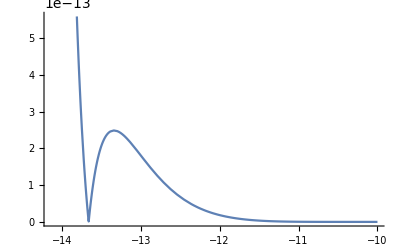

```mathematica
Plot[Re[1/Sqrt[DetSLϑ[10,30,-b]]],{b,-√((10-30)^2/2),-√((10-30)^2/4)}]
```

## Plots of Hessian, Regge action and dressed amplitude

### Plots for the Hessian

Hessian for ϑ=1 (blue) and ϑ≠1 (black) in Sector I

```mathematica
Manipulate[Plot[Re[InvSqtDetSLI[a0,a1,b]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,100},{a1,1,100}]
```

```mathematica
Manipulate[Show[{Plot[Re[1/Sqrt[DetSL[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black],Plot[Re[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue]},PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},Automatic}],{a0,1,100},{a1,1,100}]
Manipulate[Show[{Plot[Im[1/Sqrt[DetSL[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black],Plot[Im[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue]},PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},Automatic}],{a0,1,100},{a1,1,100}]
```

Visualization that measure tends to zero for lightlike trapezoid

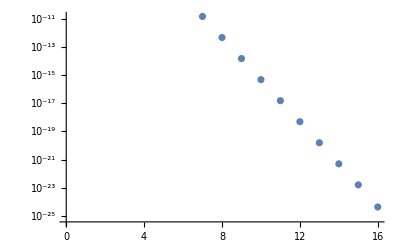

```mathematica
ListLogPlot[Table[N[InvSqtDetSLI[1,2,√((1-2)^2/4)+10^-n]],{n,0,15}]]
```

If the vartheta is added:

```mathematica
Series[ϑbSL[1,2,b]^4,{b,1/2,5}]
Series[InvSqtDetSLI[1,2,b],{b,1/2,5}]
```

16 (b-1/2)^4+64 (b-1/2)^5+O[b-1/2]^6

(b-1/2)^(3/2)/(32 √2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((33/64+ⅈ/16) (b-1/2)^(5/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((1115/256+(133 ⅈ)/64) (b-1/2)^(7/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((10937/512+(3863 ⅈ)/128) (b-1/2)^(9/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+O[b-1/2]^(11/2)

The measure times vartheta diverges as x^(-5/2) for x → 0, where at x = 0, the trapezoid is lightlike.

```mathematica
Manipulate[Plot[Re[1/ϑbSL[a0,a1,b]^4],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,10},{a1,1,10}]
```

```mathematica
=1 in Sector
```

ϑ actually leads to a polynomial divergence that cannot be cured with the polynomial decay of the inverse determinant

What happens if we change the definition of vartheta from ϑ = e^φ to ϑ = e^-φ?

```mathematica
Manipulate[Plot[Re[ϑbSL[a0,a1,b]^4/Sqrt[DetSLalt[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Black,PlotRange->{{√((a0-a1)^2/4),√((a0-a1)^2/2)},All}],{a0,1,100},{a1,1,100}]
```

```mathematica
Series[DetSLalt[1,2,b],{b,1/2,3}]
```

-(3/1024-(3 ⅈ)/1024)/(b-1/2)^16+(7/64-(3 ⅈ)/64)/(b-1/2)^15-(1695/1024+(81 ⅈ)/1024)/(b-1/2)^14+(6601/512+(4071 ⅈ)/512)/(b-1/2)^13-(12155/256+(23161 ⅈ)/256)/(b-1/2)^12-(4629/128-(17229 ⅈ)/32)/(b-1/2)^11+(345817/256-(486659 ⅈ)/256)/(b-1/2)^10-(248475/32-(115301 ⅈ)/32)/(b-1/2)^9+(13962341/512+(74091 ⅈ)/512)/(b-1/2)^8-(2337735/32+(405699 ⅈ)/16)/(b-1/2)^7+(90777041/512+(56160831 ⅈ)/512)/(b-1/2)^6-(112213979/256+(95676661 ⅈ)/256)/(b-1/2)^5+(281232771/256+(309782965 ⅈ)/256)/(b-1/2)^4-(21192427/8+(236991789 ⅈ)/64)/(b-1/2)^3+(1546283635/256+(2741505337 ⅈ)/256)/(b-1/2)^2-(1691497765/128+(3838549267 ⅈ)/128)/(b-1/2)+(28805900255/1024+(84001637473 ⅈ)/1024)-(1843138451/32+218804374 ⅈ) (b-1/2)+(113295020315/1024+(585715992629 ⅈ)/1024) (b-1/2)^2-(99323448181/512+(753962551835 ⅈ)/512) (b-1/2)^3+O[b-1/2]^4

```mathematica
Series[InvSqtDetSLI[1,2,b],{b,1/2,4}]
```

(b-1/2)^(3/2)/(32 √2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((33/64+ⅈ/16) (b-1/2)^(5/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+((1115/256+(133 ⅈ)/64) (b-1/2)^(7/2))/(√2 √(ⅈ/(-1+2 b)^3) (-1+2 b)^(3/2))+O[b-1/2]^(9/2)

```mathematica
Series[1/Sqrt[DetSLalt[1,2,b]],{b,1/2,9}]
```

(32 (b-1/2)^8)/(√3 √(-(1-ⅈ)/(-1+2 b)^16) (-1+2 b)^8)+((1280/3+(512 ⅈ)/3) (b-1/2)^9)/(√3 √(-(1-ⅈ)/(-1+2 b)^16) (-1+2 b)^8)+O[b-1/2]^10

Hessian for ϑ=1 in Sector II

```mathematica
Manipulate[Plot[{Re[1/DetSLId[a0,a1,b]],Im[1/DetSLId[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Blue,Orange},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Re[1/Sqrt[DetSLId[a0,a1,b]]],Re[InvSqtDetSLIdII[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Im[1/Sqrt[DetSLId[a0,a1,b]]],Im[InvSqtDetSLIdII[a0,a1,b]]},{b,0,√((a0-a1)^2/4)},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,√((a0-a1)^2/4)},Automatic}],{a0,1,10},{a1,1,10}]
```

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Hessian for ϑ=1 in Sector III

```mathematica
Manipulate[Plot[{Re[1/DetTLId[a0,a1,b]],Im[1/DetTLId[a0,a1,b]]},{b,0,10},PlotStyle->{Blue,Orange},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Re[1/Sqrt[DetTLId[a0,a1,b]]],Re[1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b)^3]Sqrt[ (-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3])]},{b,0,10},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
Manipulate[Plot[{Im[1/Sqrt[DetTLId[a0,a1,b]]],Im[1/(Sqrt[-32 ⅈ a0^3 a1^3]Sqrt[((-1-(a0-a1)^2/(4 b^2)) b )^3]Sqrt[(-(((-2+2 ⅈ) (a0+a1)-(a0-a1)^2/b-4 b) ((a0-a1)^2+(1+ⅈ) (a0+a1) b))/(8 b)-((a0-a1)^2 (-2 b+√(2 (a0-a1)^2+4 b^2))^2)/(16 b^2))^3])]},{b,0,10},PlotStyle->{Black,{Red,Dashed}},PlotRange->{{0,10},Automatic}],{a0,1,10},{a1,1,10}]
```

Putting I and II side by side

```mathematica
Manipulate[Show[{Plot[Re[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue],Plot[Re[InvSqtDetSLIdII[a0,a1,b]],{b,0,√((a0-a1)^2/4)},PlotStyle->Black]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,1,10},{a1,1,10}]
Manipulate[Show[{Plot[Im[1/Sqrt[DetSLId[a0,a1,b]]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)},PlotStyle->Blue],Plot[Im[InvSqtDetSLIdII[a0,a1,b]],{b,0,√((a0-a1)^2/4)},PlotStyle->Black]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,1,10},{a1,1,10}]
```

### Plots of the Regge action

Sector I

```mathematica
Manipulate[Plot[Piecewise[{{Subscript[S, I,alt][a0,a1,b],√((a0-a1)^2/4)<b<√((a0-a1)^2/2)},{Subscript[S, II][a0,a1,b],0<b<√((a0-a1)^2/4)},{Subscript[S, null][a0,a1,b],b==√((a0-a1)^2/4)}}],{b,0,√((a0-a1)^2/2)}],{a0,0,200},{a1,0,200}]
```

```mathematica
Manipulate[Show[{Plot[Subscript[S, I][a0,a1,b],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],Plot[Subscript[S, II][a0,a1,b],{b,0,√((a0-a1)^2/4)}]},PlotRange->{{0,√((a0-a1)^2/2)},All}],{a0,0,200},{a1,0,200}]
```

Sector II

```mathematica
Manipulate[Plot[Subscript[S, II][a0,a1,b],{b,0,√((a0-a1)^2/4)},PlotRange->All],{a0,0,200},{a1,0,200}]
```

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

Sector III

```mathematica
Manipulate[ListPlot[Table[Subscript[S, III][a0,a1,b],{b,1/2,100}],PlotRange->All],{a0,0,200},{a1,0,200}]
```

Sector III with matter

```mathematica
Manipulate[ListPlot[Table[Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,3,5,0.1],{b,1/2,100}],PlotRange->All],{a0,0,20},{a1,0,20}]
```

### Integrand of effective path integral

```mathematica
Subscript[A, f,tl][k_]:=2k-1;
Subscript[A, f,sl][s_]:=-EulerGamma/Pi s*Tanh[Pi*s];
(*Subscript[A, v,I][a0_,a1_,b_]:=Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,sl][b]*(InvSqtDetSLId[a0,a1,b]*Exp[-I*Subscript[S, I,alt][a0,a1,b]]+(InvSqtDetSLI[a0,a1,b]*Exp[I*Subscript[S, I,alt][a0,a1,b]])/ϑbSL[a0,a1,b]^4); wrong sign of dih. angles here*)
Subscript[A, v,I][a0_,a1_,b_]:=Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,sl][b]*(InvSqtDetSLId[a0,a1,b]*Exp[I*Subscript[S, I][a0,a1,b]]+(ϑbSL[a0,a1,b]^4*Exp[-I*Subscript[S, I][a0,a1,b]])/(√DetSLalt[a0,a1,b]));
(*This dressed vertex amplitude for Sector I is with ϑ = e^-φ where ϑ is vartheta and φ is any dihedral angle*)
Subscript[A, v,II][a0_,a1_,b_]:=Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,sl][b]*InvSqtDetSLIdII[a0,a1,b]*Exp[I*Subscript[S, II][a0,a1,b]];
Subscript[A, v,III][a0_,a1_,b_]:=Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,tl][b]*InvSqtDetTLIdIII[a0,a1,b]*Exp[I*Subscript[S, III][a0,a1,b]];
PartSumListAvIII[a0_,a1_,M_]:=Accumulate[Table[Subscript[A, v,III][a0,a1,b/2],{b,1,2M}]]
PartSumListAvIIItReg1[a0_,a1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2],{b,1,2M}]]
PartSumListAvIIIReg2[a0_,a1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2]*Exp[-b/(2M)]*Cos[b/(2M)],{b,1,2M}]]
PartSumListIII[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIReg1[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIReg2[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Exp[-b/(2M)]Cos[b/(2M)]Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIb[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIbReg1[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
PartSumListIIIbReg2[a0_,a1_,ϕ0_,ϕ1_,M_]:=Accumulate[Table[1/M^3 Exp[-b/(2M)]Cos[b/(2M)] b/2 Subscript[A, v,III][a0,a1,b/2]*Exp[-Subscript[S, ϕ,tl][a0,a1,b/2,ϕ0,ϕ1]],{b,1,2M}]]
```

```mathematica
Manipulate[Plot[Re[Subscript[A, v,I][a0,a1,b]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,100},{a1,1,100}]
Manipulate[Plot[Re[Subscript[A, v,I,alt][a0,a1,b]],{b,√((a0-a1)^2/4),√((a0-a1)^2/2)}],{a0,1,100},{a1,1,100}]
Manipulate[Plot[Re[Subscript[A, v,II][a0,a1,b]],{b,0,√((a0-a1)^2/4)},PlotRange->All],{a0,1,100},{a1,1,100}]
Manipulate[Show[{ListPlot[Table[Re[Subscript[A, v,III][a0,a1,b]],{b,1/2,50}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b]],{b,1/2,50}]}],{a0,1,100},{a1,1,100}]
```

Plot::plld: Endpoints for b in {b,0,0} must have distinct machine-precision numerical values.

```mathematica
Manipulate[Plot[(a Sin[c/(√x)])/x^2,{x,1,206}],{a,-2,2},{c,2,1000}]
```

```mathematica
Manipulate[Show[ListPlot[Table[Re[N[Subscript[A, v,ⅈ][10,20,b/100]]],{b,501,706}],PlotStyle->Red],Plot[(a Sin[c/x])/x^d,{x,1,206}]],{a,-2,2},{d,-2,2},{c,-2,2}]
```

```mathematica
Manipulate[Show[{ListPlot[Table[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]],{b,1,50}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]],{b,1,50}]}],{a0,1,100},{a1,1,100},{dϕ,0,10}]
```

```mathematica
Simplify[Series[Subscript[A, f,sl][a0]*Subscript[A, f,sl][a1]*Subscript[A, f,tl][b]*InvSqtDetTLIdIII[a0,a1,b],{b,Infinity,2}],b>0]
```

-(ⅈ a0 a1 EulerGamma^2 Tanh[a0 π] Tanh[a1 π])/(√2 √(-ⅈ a0^3 a1^3) √((-1+ⅈ) (a0+a1)^3) π^2 b^2)+O[1/b]^3

Dressed measure falls off as 1/b^2

```mathematica
Manipulate[Plot[Piecewise[{{Re[Subscript[A, v,II][a0,a1,b]],0<b<√((a0-a1)^2/4)},{Re[Subscript[A, v,I][a0,a1,b]],√((a0-a1)^2/4)<b<√((a0-a1)^2/2)}}],{b,0,√((a0-a1)^2/2)},PlotRange->All,Epilog->InfiniteLine[{{√((a0-a1)^2/4),0},{-1,1}}]],{a0,1,100},{a1,1,100}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Re[Subscript[A, v,I,alt][a0,a1,-b]],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)},{Re[Subscript[A, v,II][a0,a1,-b]],-√((a0-a1)^2/4)<b<0},{Re[Subscript[A, v,III][a0,a1,b]],b>0}}],{b,-√((a0-a1)^2/2),100},PlotRange->{{-√((a0-a1)^2/2),100},{-10^-8,10^-8}},Epilog->InfiniteLine[{{-√((a0-a1)^2/4),0},{-1,1}}]],{a0,1,100},{a1,1,100}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Re[Subscript[A, v,I,alt][a0,a1,-b]*Exp[-I Subscript[S, ϕ,sl][a0,a1,b,0,1.7]]],-√((a0-a1)^2/2)<b<-√((a0-a1)^2/4)},{Re[Subscript[A, v,II][a0,a1,-b]*Exp[-I Subscript[S, ϕ,sl][a0,a1,b,0,1.7]]],-√((a0-a1)^2/4)<b<0},{Re[Subscript[A, v,III][a0,a1,b]*Exp[-I Subscript[S, ϕ,tl][a0,a1,b,0,1.7]]*Exp[-I*Λ*b]],b>0}}],{b,-√((a0-a1)^2/2),200},PlotRange->{{-√((a0-a1)^2/2),200},{-2*10^-9,2*10^-9}},Epilog->InfiniteLine[{{-√((a0-a1)^2/4),0},{-1,1}}]],{a0,1,100},{a1,1,100},{Λ,0,1}]
```

```mathematica
ZI=NIntegrate[Subscript[A, v,I,alt][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/2),√((10-30)^2/4)},Method->"LocalAdaptive"]
ZII=NIntegrate[Subscript[A, v,II][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/4),0},Method->"LocalAdaptive"]
ZIII=Sum[Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

1.17685×10^-13-4.54926×10^-12 ⅈ

5.43804×10^-12-4.33981×10^-12 ⅈ

-3.52081×10^-8+5.66125×10^-8 ⅈ

```mathematica
ZIII=Sum[Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

-3.52081×10^-8+5.66125×10^-8 ⅈ

```mathematica
ZbI=NIntegrate[b*Subscript[A, v,I,alt][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/2),√((10-30)^2/4)},Method->"LocalAdaptive"]
ZbII=NIntegrate[b*Subscript[A, v,II][10,30,b]*Exp[-I*Subscript[S, ϕ,sl][10,30,b,0,1.7]],{b,√((10-30)^2/4),0},Method->"LocalAdaptive"]
```

1.04011×10^-12-4.54891×10^-11 ⅈ

5.96258×10^-11-4.60865×10^-11 ⅈ

```mathematica
ZbIII=Sum[b/2 Subscript[A, v,III][10,30,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,30,b/2,0,1.7]],{b,1,10000}]
```

-0.000020821-0.0000193952 ⅈ

```mathematica
(ZbI+ZbII+ZbIII)/(ZI+ZII+ZIII)
```

-82.1247+418.912 ⅈ

```mathematica
ZbIII/ZIII
```

-82.11+418.846 ⅈ

## Attempts to compute Z with freezing oscillations

### Identifying saddle points

```mathematica
Manipulate[ListPlot[Table[-Subscript[S, III][a0,a1,b/2]-Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0],{b,1,50}],PlotRange->All],{a0,1,50},{a1,1,50},{dϕ,0,1}]
Manipulate[Show[{ListPlot[Table[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0]]],{b,1,200}],PlotStyle->Red],Plot[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ,0]]],{b,1,200}]}],{a0,1,50},{a1,1,50},{dϕ,0,1}]
```

```mathematica
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,0,dϕ],b]/.{a0->30,a1->50,dϕ->0.85})==0,{b,25}]
```

{b→20.7964}

```mathematica
Table[NSum[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->40,dϕ->0.7}),{b,1,Infinity},NSumTerms->200],{M,10,15}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {4.81039×10^7}. NIntegrate obtained -6.4988×10^-9-1.29652×10^-9 ⅈ and 1.67673×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {4.81039×10^7}. NIntegrate obtained -7.8962×10^-9-2.10824×10^-9 ⅈ and 2.6656×10^-14 for the integral and error estimates.

{-3.87609×10^-9+4.24413×10^-9 ⅈ,ComplexInfinity,-4.30502×10^-9+4.008×10^-9 ⅈ,-4.53129×10^-9+3.94585×10^-9 ⅈ,ComplexInfinity,-5.32096×10^-9+3.7639×10^-9 ⅈ}

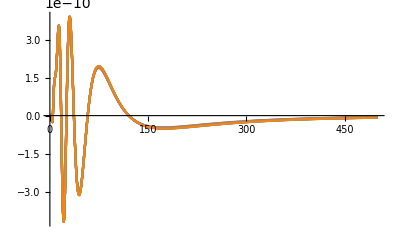

```mathematica
Show[Table[Plot[Re[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->40,dϕ->0.7})],{b,1,500},PlotStyle->ColorData[97,M+1],PlotRange->All],{M,10,20}],PlotLegends->Automatic]
```

```mathematica
Msums=Table[Sum[(Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->50,dϕ->0.85}),{b,1,1000}],{M,1,30}]
```

{2.60358×10^-9+2.93703×10^-9 ⅈ,2.01763×10^-9+5.72367×10^-9 ⅈ,8.13228×10^-10+6.73695×10^-9 ⅈ,-2.16438×10^-10+7.0876×10^-9 ⅈ,-1.03242×10^-9+7.18255×10^-9 ⅈ,-1.67523×10^-9+7.17704×10^-9 ⅈ,-2.18703×10^-9+7.13297×10^-9 ⅈ,-2.60066×10^-9+7.07596×10^-9 ⅈ,-2.94012×10^-9+7.01685×10^-9 ⅈ,-3.22273×10^-9+6.96011×10^-9 ⅈ,-3.46112×10^-9+6.90747×10^-9 ⅈ,-3.66457×10^-9+6.85938×10^-9 ⅈ,-3.84001×10^-9+6.81575×10^-9 ⅈ,-3.99272×10^-9+6.77625×10^-9 ⅈ,-4.12675×10^-9+6.74049×10^-9 ⅈ,-4.24527×10^-9+6.70808×10^-9 ⅈ,-4.35077×10^-9+6.67862×10^-9 ⅈ,-4.44525×10^-9+6.65179×10^-9 ⅈ,-4.53033×10^-9+6.62729×10^-9 ⅈ,-4.60733×10^-9+6.60483×10^-9 ⅈ,-4.67733×10^-9+6.58421×10^-9 ⅈ,-4.74123×10^-9+6.5652×10^-9 ⅈ,-4.7998×10^-9+6.54765×10^-9 ⅈ,-4.85366×10^-9+6.5314×10^-9 ⅈ,-4.90335×10^-9+6.51631×10^-9 ⅈ,-4.94934×10^-9+6.50226×10^-9 ⅈ,-4.99203×10^-9+6.48917×10^-9 ⅈ,-5.03175×10^-9+6.47693×10^-9 ⅈ,-5.0688×10^-9+6.46547×10^-9 ⅈ,-5.10344×10^-9+6.45472×10^-9 ⅈ}

```mathematica
Msumsb=Table[Sum[((b/2)Exp[-b/(2M*50)]Cos[b/(2M*50)]Subscript[A, v,III][a0,a1,b/2]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b/2,0,dϕ]]/.{a0->30,a1->50,dϕ->0.85}),{b,1,1000}],{M,1,30}]
```

{8.79928×10^-8+9.66137×10^-8 ⅈ,-8.86143×10^-9+2.48271×10^-7 ⅈ,-1.69082×10^-7+2.86273×10^-7 ⅈ,-3.28394×10^-7+2.58582×10^-7 ⅈ,-4.69516×10^-7+2.05351×10^-7 ⅈ,-5.88965×10^-7+1.47005×10^-7 ⅈ,-6.88681×10^-7+9.16128×10^-8 ⅈ,-7.7194×10^-7+4.17312×10^-8 ⅈ,-8.41881×10^-7-2.27643×10^-9 ⅈ,-9.01128×10^-7-4.08413×10^-8 ⅈ,-9.51767×10^-7-7.46247×10^-8 ⅈ,-9.95431×10^-7-1.04299×10^-7 ⅈ,-1.0334×10^-6-1.30474×10^-7 ⅈ,-1.06666×10^-6-1.5367×10^-7 ⅈ,-1.09602×10^-6-1.74329×10^-7 ⅈ,-1.12209×10^-6-1.92818×10^-7 ⅈ,-1.14539×10^-6-2.09443×10^-7 ⅈ,-1.16633×10^-6-2.24459×10^-7 ⅈ,-1.18524×10^-6-2.38079×10^-7 ⅈ,-1.20239×10^-6-2.50483×10^-7 ⅈ,-1.21801×10^-6-2.6182×10^-7 ⅈ,-1.2323×10^-6-2.72219×10^-7 ⅈ,-1.24542×10^-6-2.81789×10^-7 ⅈ,-1.2575×10^-6-2.90622×10^-7 ⅈ,-1.26866×10^-6-2.98798×10^-7 ⅈ,-1.279×10^-6-3.06387×10^-7 ⅈ,-1.28861×10^-6-3.13449×10^-7 ⅈ,-1.29755×10^-6-3.20035×10^-7 ⅈ,-1.30591×10^-6-3.26192×10^-7 ⅈ,-1.31372×10^-6-3.31959×10^-7 ⅈ}

```mathematica
SequenceLimit[Msumsb]/SequenceLimit[Msums]
```

78.7011+157.443 ⅈ

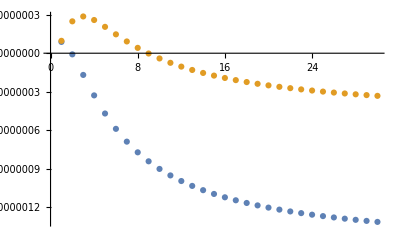

```mathematica
ListPlot[{Re[Msumsb],Im[Msumsb]}]
```

```mathematica
limitsZ=Table[SequenceLimit[PartSumListIIIReg1[30,40,0,0.7,1000+1000*n]],{n,0,5}]
limitsZb=Table[SequenceLimit[PartSumListIIIbReg1[30,40,0,0.7,1000+1000*n]],{n,0,5}]
```

{1.17622×10^-19-4.80783×10^-18 ⅈ,1.19512×10^-20-6.24266×10^-19 ⅈ,2.3394×10^-21-1.87459×10^-19 ⅈ,1.65078×10^-21-7.78721×10^-20 ⅈ,6.8791×10^-22-4.02188×10^-20 ⅈ,3.54165×10^-22-2.33961×10^-20 ⅈ}

{-1.60517×10^-15-3.94774×10^-15 ⅈ,-2.49192×10^-16-7.80175×10^-16 ⅈ,1.0159×10^-17-2.32801×10^-16 ⅈ,-2.55202×10^-17-8.95563×10^-17 ⅈ,-1.28882×10^-17-4.71119×10^-17 ⅈ,-8.02932×10^-18-2.88365×10^-17 ⅈ}

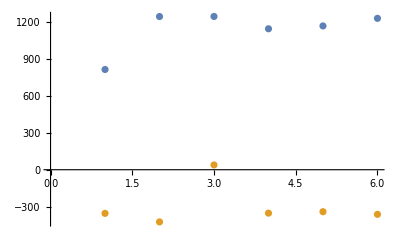

```mathematica
ListPlot[{Re[Table[limitsZb[[i]]/limitsZ[[i]],{i,1,6}]],Im[Table[limitsZb[[i]]/limitsZ[[i]],{i,1,6}]]}]
```

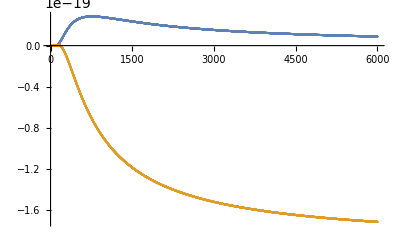

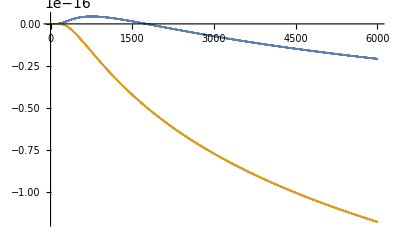

```mathematica
ListPlot[{Re[PartSumListIIIReg1[30,40,0,0.7,3000]],Im[PartSumListIIIReg1[30,40,0,0.7,3000]]}]
ListPlot[{Re[PartSumListIIIbReg1[30,40,0,0.7,3000]],Im[PartSumListIIIbReg1[30,40,0,0.7,3000]]}]
```

### Partition sum and expectation value for a_0=10,a_1=20,ϕ_0=3,ϕ_1=5 in Sector III

```mathematica
Manipulate[ListPlot[Table[(-Subscript[S, III][a0,a1,b]-Subscript[S, ϕ,tl][a0,a1,b,0,dϕ])/.{a0->10,a1->30},{b,1/2,100}],PlotRange->All],{dϕ,0,10}]
```

```mathematica
4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,0,1.7],b]/.{a0->10,a1->30}
FindRoot[-(577.9999999999999 b)/((200+b^2)^(3/2))+4 (π/2-ArcCos[400/(400+4 b^2)])==0,{b,20}]
```

-(578. b)/((200+b^2)^(3/2))+4 (π/2-ArcCos[400/(400+4 b^2)])

{b→20.7964}

Comparing Z for different regulators

```mathematica
PartZ=N[PartSumListIII[10,20,1,2,300]];
PartZReg1=N[PartSumListIIIReg1[10,20,1,2,300]];
PartZReg2=N[PartSumListIIIReg2[10,20,1,2,300]];
```

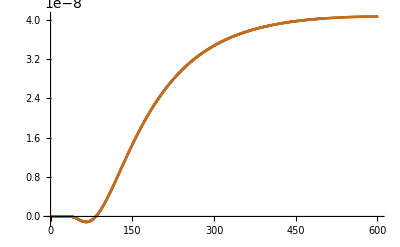

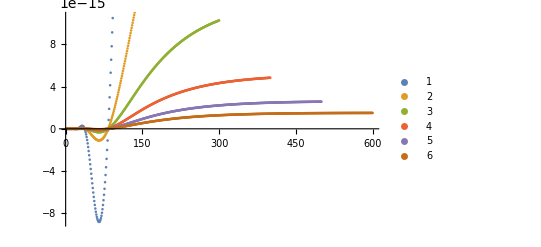

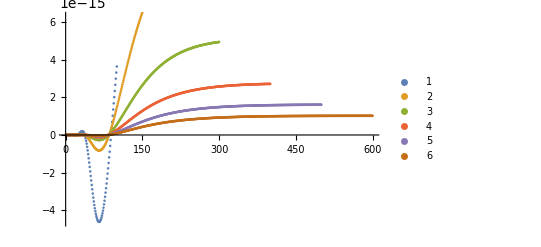

```mathematica
ListPlot[Table[N[Re[PartSumListIII[10,20,1,2,50+50n]]],{n,0,5}]]
ListPlot[Table[N[Re[PartSumListIIIReg1[10,20,1,2,50+50n]]],{n,0,5}],PlotLegends->Automatic]
ListPlot[Table[N[Re[PartSumListIIIReg2[10,20,1,2,50+50n]]],{n,0,5}],PlotLegends->Automatic]
```

Getting limit values of M → ∞

```mathematica
Z=SequenceLimit[PartZ]
ZReg1=SequenceLimit[PartZReg1]
ZReg2=SequenceLimit[PartZReg2]
```

3.31756×10^-8-7.54712×10^-8 ⅈ

1.22401×10^-15-2.79789×10^-15 ⅈ

1.01258×10^-15-7.6698×10^-16 ⅈ

Getting the expectation value of b

```mathematica
PartExpb=N[PartSumListIIIb[10,20,1,2,300]];
PartExpbReg1=N[PartSumListIIIbReg1[10,20,1,2,300]];
PartExpbReg2=N[PartSumListIIIbReg2[10,20,1,2,300]];
```

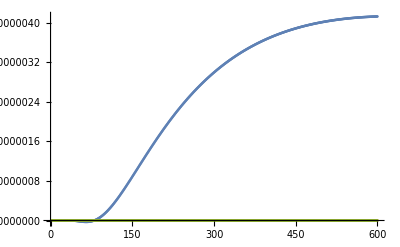

```mathematica
ListPlot[{Re[PartExpb],Re[PartExpbReg1],Re[PartExpbReg2]}]
```

```mathematica
ExpbI=SequenceLimit[PartExpb]
ExpbIReg1=SequenceLimit[PartExpbReg1]
ExpbIReg2=SequenceLimit[PartExpbReg2]
```

-1.7814×10^-6-0.0000312571 ⅈ

-6.4403×10^-14-1.13793×10^-12 ⅈ

9.33024×10^-14-1.47301×10^-13 ⅈ

```mathematica
ExpbI/Z
ExpbIReg1/ZReg1
```

338.395-172.355 ⅈ

332.924-168.665 ⅈ

### Partition sum and expectation value for a_0=10,a_1=20,ϕ_0=3,ϕ_1=5 including Sector I and II

```mathematica
(*NIntegrate[Subscript[A, v,II][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,0,5},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo"]
NIntegrate[b^2*Subscript[A, v,II][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,0,5},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo"]*)
NIntegrate[Subscript[A, v,I,alt][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,3]],{b,5,10/(√2)},Exclusions->{b==10/(√2)},Method->"LocalAdaptive"]
(*NIntegrate[b^2*Subscript[A, v,I][10,20,b]*Exp[-I*Subscript[S, ϕ,sl][10,20,b,1,2]],{b,5,10/(√2)},Exclusions->(b==5),Method->"AdaptiveQuasiMonteCarlo",MinRecursion->20,MaxRecursion->500]*)
```

-2.30281×10^-11-1.71437×10^-10 ⅈ

```mathematica
(-3.3414150643675096*^-9-5.273216877892166*^-10 ⅈ+9.314213482194513*^39+2.164076237576497*^37 ⅈ+-1.7813952468589908*^-6-0.000031257065076168984 ⅈ)/(3.3175591967997243*^-8-7.547117889642238*^-8 ⅈ+-1.3106876484265184*^-10-3.0107014695590344*^-11 ⅈ+3.7256853928777185*^38+8.656304950284823*^35 ⅈ)
```

25.+1.40672×10^-13 ⅈ

-Graphics3D-

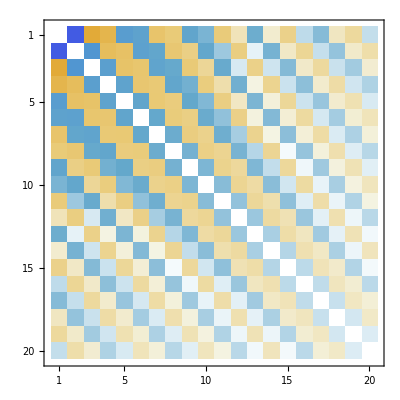

```mathematica
MatrixPlot[%226]
```

Evaluating the timelike partition sum

```mathematica
ResourceFunction["SequenceLimit"][PartSumList[1,2,100],Method->"Wynn]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[]

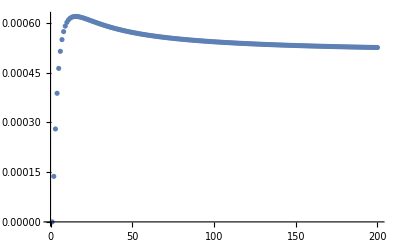

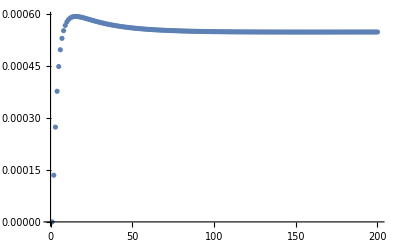

```mathematica
ListPlot[Re[PartSumList[1,2,100]]]
ListPlot[Re[PartSumListReg[1,2,100]]]
```

```mathematica
SequenceLimit[N[Re[PartSumList[1,2,300]]]]
SequenceLimit[N[Re[PartSumListReg[1,2,300]]]]
```

0.000507816

0.000533483

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

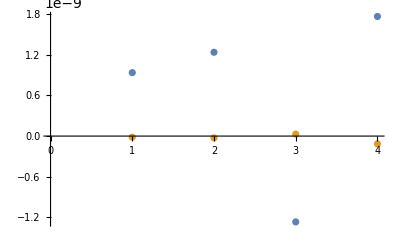

```mathematica
ListPlot[{Table[SequenceLimit[N[Re[PartSumList[10,50,100+50*n]]]],{n,0,3}],Table[SequenceLimit[N[Re[PartSumListReg[10,50,100+50*n]]]],{n,0,3}]}]
```

```mathematica
SequenceLimit[N[Re[PartSumList[1,2,200]]]]
SequenceLimit[N[Re[PartSumListReg[1,2,200]]],Method->"WynnEpsilon"]
```

0.000508771

0.000539656

```mathematica
Subscript[S, ϕ][10,20,201,3,5]
```

S_ϕ[10,20,201,3,5]

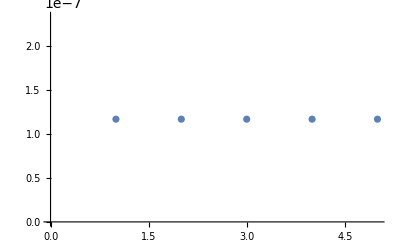

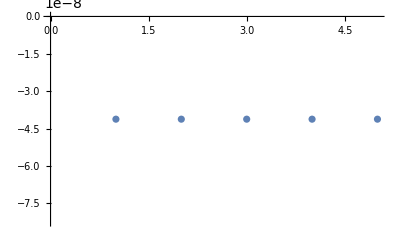

```mathematica
ListPlot[Table[Re[NSum[Subscript[A, v,III][10,20,b/2],{b,1,Infinity},NSumTerms->(100+50*n)]],{n,0,4}]]
ListPlot[Table[Re[NSum[Subscript[A, v,III][10,20,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,20,b/2,3,5]],{b,1,Infinity},NSumTerms->(100+50*n)]],{n,0,4}]]
```

```mathematica
Im[NSum[Subscript[A, v,III][10,20,b/2]*Exp[-I*Subscript[S, ϕ,tl][10,20,b/2,5,3]],{b,1,Infinity},NSumTerms->150]]
```

2.15413×10^-8

```mathematica
4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,3,5],b]/.{a0->10,a1->20};
FindRoot[-(450 b)/((50+b^2)^(3/2))+4 (π/2-ArcCos[100/(100+4 b^2)])==0,{b,5}]
```

{b→3.26302}

```mathematica
NLimit[PartSumList[1,2,M],M->Infinity]
```

Table::iterb: Iterator {b,1,2 M} does not have appropriate bounds.

Table::iterb: Iterator {b+A_(v,III)[1,2,b/2],1+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b Plus[«2»]-4 ArcSinh[«1»])) EulerGamma^2 Tanh[π] «1»)/(2 √2 √((-1+Times[«2»])^3 b^3) √((-1/4 Plus[«3»] Power[«2»] Plus[«2»]-1/4 Power[«2»] Power[«2»])^3) π^2),2 M+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b Plus[«2»]-4 ArcSinh[«1»])) EulerGamma^2 Tanh[π] «1»)/(2 √2 √((-1+Times[«2»])^3 b^3) √((-1/4 Plus[«3»] Power[«2»] Plus[«2»]-1/4 Power[«2»] Power[«2»])^3) π^2)} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::write: Tag Plus in b+A_(v,III)[1,2,b/2] is Protected.

Table::write: Tag Plus in b+A_(v,III)[1.,2.,b 0.5] is Protected.

General::stop: Further output of Table::write will be suppressed during this calculation.

NLimit::notnum: The expression Table[A_(v,III)[1.,2.,b 0.5],{b+A_(v,III)[1.,2.,b 0.5],1.+((0.00840797+0.00840797 ⅈ) 2.71828^((0.-1. ⅈ) (Times[«3»]+Times[«2»])) (-1.+b))/(√(Plus[«2»]^3 b^3) √((Times[«4»]+Times[«3»])^3)),2.+((0.00840797+0.00840797 ⅈ) 2.71828^((0.-1. ⅈ) (Times[«3»]+Times[«2»])) (-1.+b))/(√(Plus[«2»]^3 b^3) √((Times[«4»]+Times[«3»])^3))}] is not numerical at the point M == 1..

NLimit[Table[A_(v,III)[1,2,b/2],{b+A_(v,III)[1,2,b/2],1+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b (π/2-ArcCos[1/(1+b^2)])-4 ArcSinh[1/(√(1+b^2))])) EulerGamma^2 Tanh[π] Tanh[2 π])/(2 √2 √((-1-1/b^2)^3 b^3) √((-(((-6+6 ⅈ)-2/b-2 b) (1+(3/2+(3 ⅈ)/2) b))/(4 b)-((-b+√(2+b^2))^2)/(4 b^2))^3) π^2),2 M+((-1)^(1/4) (-1+b) ⅇ^(-ⅈ (2 b (π/2-ArcCos[1/(1+b^2)])-4 ArcSinh[1/(√(1+b^2))])) EulerGamma^2 Tanh[π] Tanh[2 π])/(2 √2 √((-1-1/b^2)^3 b^3) √((-(((-6+6 ⅈ)-2/b-2 b) (1+(3/2+(3 ⅈ)/2) b))/(4 b)-((-b+√(2+b^2))^2)/(4 b^2))^3) π^2)}],M→∞]

```mathematica
ResourceFunction["SequenceLimit"][]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[]

```mathematica
ResourceSearch["SequenceLimit"]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

ResourceSearch::invloc: The specified search location … is invalid, Use a list containing PersistenceLocation objects or URL objects for resource systems.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Indeterminate

```mathematica
ResourceFunction["SequenceLimit"][Accumulate[Table[(-1)^n/n,{n,1,10}]]]
```

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[Accumulate[Table[(-1)^n/n,{n,1,10}]]]

```mathematica
NSum[Subscript[A, v,III][1,2,b/2],{b,1,Infinity}]
PartSumList[1,2,100]
ResourceFunction["SequenceLimit"][PartSumList[1,2,100],Method->"WynnEpsilon"]
```

0.000506053-0.00144881 ⅈ

{0,-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2),-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2)-(3 (-1)^(3/4) √(3/5) ⅇ^(-ⅈ (6 (π/2-ArcCos[1/10])-4 ArcSinh[1/(√10)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(20 ((145/18+2 ⅈ)-1/36 (-3+√11)^2)^(3/2) π^2),-((-1)^(3/4) ⅇ^(-ⅈ (4 (π/2-ArcCos[1/5])-4 ArcSinh[1/(√5)])) EulerGamma^2 Tanh[π] Tanh[2 π])/(5 √5 ((31/4+(9 ⅈ)/8)-1/16 (-2+√6)^2)^(3/2) π^2)-(3 (-1)^(3/4) √(3/5) ⅇ^(-ⅈ (1)) EulerGamma^2 Tanh[π] Tanh[2 π])/(20 ((145/18+2 ⅈ)-1/36 1^2)^(3/2) π^2)-(6 (-1)^(3/4) √(2/17) ⅇ^(-ⅈ (8 (π/2-1)-4 1)) EulerGamma^2 Tanh[π] Tanh[2 π])/(17 ((275/32+(45 ⅈ)/16)-1/64 (1)^2)^(3/2) π^2),192,1,1,1,1}
 |  |  |  |

Join::heads: Heads List and If at positions 1 and 3 are expected to be the same.

$Failed[PartSumList[1,2,100],Method→WynnEpsilon]

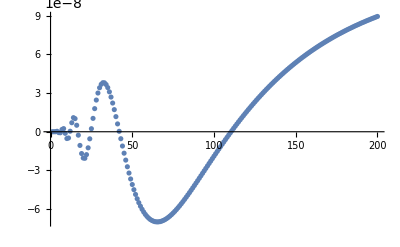

```mathematica
ListPlot[Re[PartSumList[10,20,100]]]
```

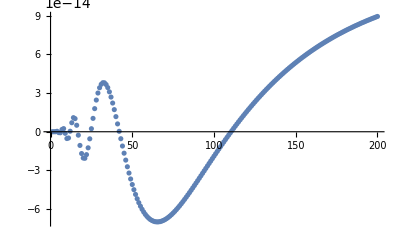

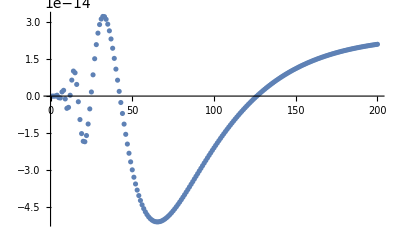

```mathematica
ListPlot[Re[PartSumListReg1[10,20,100]]]
ListPlot[Re[PartSumListReg2[10,20,100]]]
```

```mathematica
ListPlot[Table[N[Re[PartSumList[10,20,50+50n]]],{n,0,5}]]
seq2=N[Re[PartSumListReg1[10,20,300]]];
seq3=N[Re[PartSumListReg2[10,20,300]]];
SequenceLimit[seq1]
SequenceLimit[seq2]
SequenceLimit[seq3]
```

1.21707×10^-7

1.21535×10^-13

2.51364×10^-14

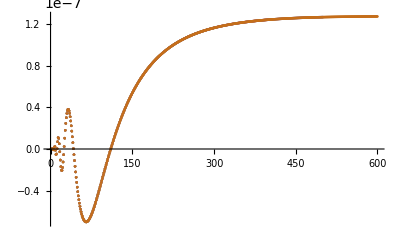

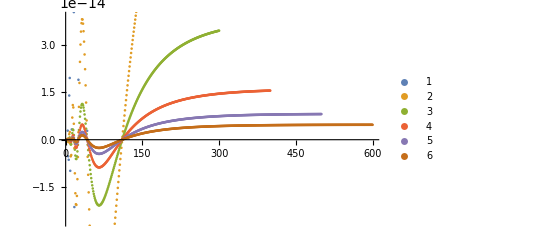

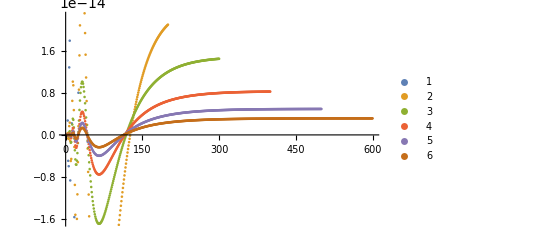

```mathematica
ListPlot[Table[N[Re[PartSumList[10,20,50+50n]]],{n,0,5}]]
ListPlot[Table[N[Re[PartSumListReg1[10,20,50+50n]]],{n,0,5}],PlotLegends->Automatic]
ListPlot[Table[N[Re[PartSumListReg2[10,20,50+50n]]],{n,0,5}],PlotLegends->Automatic]
```

```mathematica
seq2=N[Re[PartSumListReg1[10,20,300]]];
seq3=N[Re[PartSumListReg2[10,20,300]]];
SequenceLimit[seq2]
SequenceLimit[seq3]
```

4.70848×10^-15

3.15226×10^-15

```mathematica
seq3
```

{0.,-2.6233×10^-17,7.05069×10^-18,3.498×10^-16,-6.36132×10^-16,-7.68852×10^-16,1.67582×10^-15,2.3404×10^-15,-1.15569×10^-15,-4.97622×10^-15,-4.58314×10^-15,3.39613×10^-16,6.49277×10^-15,1.01594×10^-14,9.46241×10^-15,4.73056×10^-15,-2.30415×10^-15,-9.53867×10^-15,-1.52357×10^-14,-1.83502×10^-14,-1.8542×10^-14,-1.60207×10^-14,-1.13387×10^-14,-5.20268×10^-15,1.66771×10^-15,8.63×10^-15,1.51652×10^-14,2.08922×10^-14,2.5562×10^-14,2.90407×10^-14,3.12875×10^-14,3.23323×10^-14,3.22551×10^-14,3.11687×10^-14,2.92043×10^-14,2.65007×10^-14,2.31962×10^-14,1.9423×10^-14,1.53037×10^-14,1.0949×10^-14,6.45675×10^-15,1.9116×10^-15,-2.61434×10^-15,-7.06098×10^-15,-1.13792×10^-14,-1.55297×10^-14,-1.94821×10^-14,-2.32137×10^-14,-2.67082×10^-14,-2.99553×10^-14,-3.29491×10^-14,-3.5688×10^-14,-3.81734×10^-14,-4.04095×10^-14,-4.24026×10^-14,-4.41605×10^-14,-4.56924×10^-14,-4.70083×10^-14,-4.81187×10^-14,-4.90348×10^-14,-4.97677×10^-14,-5.03288×10^-14,-5.0729×10^-14,-5.09795×10^-14,-5.10907×10^-14,-5.10732×10^-14,-5.09368×10^-14,-5.06911×10^-14,-5.03451×10^-14,-4.99075×10^-14,-4.93865×10^-14,-4.87897×10^-14,-4.81246×10^-14,-4.73979×10^-14,-4.66161×10^-14,-4.5785×10^-14,-4.49104×10^-14,-4.39975×10^-14,-4.3051×10^-14,-4.20755×10^-14,-4.10751×10^-14,-4.00538×10^-14,-3.9015×10^-14,-3.79621×10^-14,-3.68981×10^-14,-3.58257×10^-14,-3.47476×10^-14,-3.3666×10^-14,-3.25831×10^-14,-3.15008×10^-14,-3.04209×10^-14,-2.9345×10^-14,-2.82746×10^-14,-2.7211×10^-14,-2.61553×10^-14,-2.51087×10^-14,-2.40721×10^-14,-2.30464×10^-14,-2.20323×10^-14,-2.10304×10^-14,-2.00414×10^-14,-1.90658×10^-14,-1.8104×10^-14,-1.71564×10^-14,-1.62234×10^-14,-1.53051×10^-14,-1.44018×10^-14,-1.35136×10^-14,-1.26408×10^-14,-1.17834×10^-14,-1.09414×10^-14,-1.01148×10^-14,-9.30378×10^-15,-8.50816×10^-15,-7.72792×10^-15,-6.96299×10^-15,-6.21327×10^-15,-5.47866×10^-15,-4.75903×10^-15,-4.05423×10^-15,-3.36412×10^-15,-2.68854×10^-15,-2.0273×10^-15,-1.38023×10^-15,-7.47136×10^-16,-1.27825×10^-16,4.77904×10^-16,1.07026×10^-15,1.64945×10^-15,2.21568×10^-15,2.76918×10^-15,3.31015×10^-15,3.83882×10^-15,4.3554×10^-15,4.86012×10^-15,5.3532×10^-15,5.83485×10^-15,6.30529×10^-15,6.76474×10^-15,7.21341×10^-15,7.65152×10^-15,8.07929×10^-15,8.49692×10^-15,8.90462×10^-15,9.30259×10^-15,9.69105×10^-15,1.00702×10^-14,1.04402×10^-14,1.08013×10^-14,1.11537×10^-14,1.14975×10^-14,1.1833×10^-14,1.21603×10^-14,1.24796×10^-14,1.27911×10^-14,1.30949×10^-14,1.33913×10^-14,1.36804×10^-14,1.39624×10^-14,1.42374×10^-14,1.45056×10^-14,1.47671×10^-14,1.50222×10^-14,1.52709×10^-14,1.55133×10^-14,1.57498×10^-14,1.59803×10^-14,1.6205×10^-14,1.64241×10^-14,1.66376×10^-14,1.68458×10^-14,1.70488×10^-14,1.72466×10^-14,1.74393×10^-14,1.76272×10^-14,1.78104×10^-14,1.79888×10^-14,1.81627×10^-14,1.83322×10^-14,1.84973×10^-14,1.86582×10^-14,1.8815×10^-14,1.89677×10^-14,1.91165×10^-14,1.92615×10^-14,1.94027×10^-14,1.95402×10^-14,1.96742×10^-14,1.98047×10^-14,1.99318×10^-14,2.00556×10^-14,2.01761×10^-14,2.02935×10^-14,2.04078×10^-14,2.05191×10^-14,2.06275×10^-14,2.0733×10^-14,2.08357×10^-14,2.09357×10^-14,2.1033×10^-14}

1.27807×10^-7

```mathematica
NSum[Re[Subscript[A, v,III][10,20,b/2]],{b,1,Infinity},Method->"WynnEpsilon",NSumTerms->1200,AccuracyGoal->10,PrecisionGoal->10]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

1.19713×10^-7

### Spacelike bulk slice

```mathematica
w[a0_,a1_,b0_]:=(a0+a1)^2/(8 √((a0-a1)^2/2+b0^2));
ϕintegral[a0_,a1_,a2_,b0_,b1_,ϕ0_,ϕ2_]:=√((I*Pi)/(w[a0,a1,b0]+w[a1,a2,b1]))Exp[-I*(ϕ0-ϕ2)^2*(w[a0,a1,b0]*w[a1,a2,b1])/(w[a0,a1,b0]+w[a1,a2,b1])];
```

```mathematica
Simplify[Series[Subscript[S, III][a0,a1,b],{a1,Infinity,2}],b>0&&a0>0&&a1>0]
Simplify[Series[Subscript[S, ϕ,tl][a0,a1,b,ϕ1,ϕ2],{a1,Infinity,2}],b>0&&a0>0&&a1>0]
```

-4 ArcSinh[1] a1+(2 b π+4 a0 ArcSinh[1])-(4 (√2 b^2))/a1-(4 (√2 a0 b^2))/a1^2+O[1/a1]^3

((ϕ1-ϕ2)^2 a1)/(4 √2)+(3 a0 (ϕ1-ϕ2)^2)/(4 √2)+((4 a0^2-b^2) (ϕ1-ϕ2)^2)/(4 √2 a1)+(a0 (4 a0^2-5 b^2) (ϕ1-ϕ2)^2)/(4 √2 a1^2)+O[1/a1]^3

```mathematica
Manipulate[Plot[Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,0,dϕ],{a1,0,100},PlotRange->All],{a0,0,10},{b,0,100},{dϕ,0,10}]
Manipulate[Plot[4ArcSinh[(a0-a1)/(√(4 b^2+(a0-a1)^2))]-4ArcSinh[(a0-a1)/(√(4 b^2+(a0-a1)^2))]+-((-a0+a1) (a0+a1)^2 dϕ^2)/(16 (1/2 (a0-a1)^2+b^2)^(3/2))+((a0+a1) dϕ^2)/(4 √(1/2 (a0-a1)^2+b^2)),{a1,0,100}],{a0,0,10},{b,0,100},{dϕ,0,10}]
```

```mathematica
Subscript[A, v,III][a0,a1,b0]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b,ϕ0,ϕ1]]*Subscript[A, v,III][a1,a2,b1]*Exp[-I*Subscript[S, ϕ,tl][a1,a2,b1,ϕ1,ϕ2]]/.{a0->20,a2->40,ϕ0->1,ϕ2->2}
```

(ⅈ (-1+2 b0) (-1+2 b1) ⅇ^(-(ⅈ (20+a1)^2 (1-ϕ1)^2)/(8 √(1/2 (20-a1)^2+b^2))-(ⅈ (40+a1)^2 (-2+ϕ1)^2)/(8 √(1/2 (-40+a1)^2+b1^2))-ⅈ (4 b0 (π/2-ArcCos[(20-a1)^2/((20-a1)^2+4 b0^2)])-4 (20-a1) ArcSinh[(20-a1)/(√((20-a1)^2+4 b0^2))])-ⅈ (4 b1 (π/2-ArcCos[(-40+a1)^2/((-40+a1)^2+4 b1^2)])-4 (-40+a1) ArcSinh[(-40+a1)/(√((-40+a1)^2+4 b1^2))])) EulerGamma^4 Tanh[20 π] Tanh[40 π] Tanh[a1 π]^2)/(640 √2 a1 √((-1-(20-a1)^2/(4 b0^2))^3 b0^3) √((-(((-2+2 ⅈ) (20+a1)-(20-a1)^2/b0-4 b0) ((20-a1)^2+(1+ⅈ) (20+a1) b0))/(8 b0)-((20-a1)^2 (-2 b0+√(2 (20-a1)^2+4 b0^2))^2)/(16 b0^2))^3) √((-1-(-40+a1)^2/(4 b1^2))^3 b1^3) √((-(((-2+2 ⅈ) (40+a1)-(-40+a1)^2/b1-4 b1) ((-40+a1)^2+(1+ⅈ) (40+a1) b1))/(8 b1)-((-40+a1)^2 (-2 b1+√(2 (-40+a1)^2+4 b1^2))^2)/(16 b1^2))^3) π^4)

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][1,a1,b0]],{a1,1/4,10},PlotRange->Full],{b0,1/2,10},{b1,1/2,10},{ϕ1,0,10}]
```

```mathematica
Manipulate[Plot[Re[(Subscript[A, v,III][a0,a1,b0]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,b0,ϕ0,ϕ1]]*Subscript[A, v,III][a1,a2,b1]*Exp[-I*Subscript[S, ϕ,tl][a1,a2,b1,ϕ1,ϕ2]]/.{a0->20,a2->20,ϕ0->1,ϕ2->5})],{a1,1/4,50},PlotRange->Full,PlotPoints->200,MaxRecursion->2],{b0,1/2,10},{b1,1/2,10},{ϕ1,0,10}]
```

```mathematica
Manipulate[Plot[Re[(Subscript[A, v,III][a0,a1,b0]*Subscript[A, v,III][a1,a2,b1]*ϕintegral[a0,a1,a2,b0,b1,ϕ0,ϕ2]/.{a0->20,a2->20,ϕ0->1,ϕ2->5})],{a1,1/4,50},PlotRange->Full,PlotPoints->200,MaxRecursion->2],{b0,1/2,10},{b1,1/2,10}]
```

```mathematica
ListPointPlot3D[Table[NIntegrate[Subscript[A, v,III][a0,a1,b0/2]*Subscript[A, v,III][a1,a2,b1/2]*ϕintegral[a0,a1,a2,b0/2,b1/2,ϕ0,ϕ2]/.{a0->20,a2->20,ϕ0->1,ϕ2->5},{a1,1/4,Infinity},Method->"AdaptiveQuasiMonteCarlo"],{b0,1,40},{b1,1,40}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.999467}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.999762}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.998802}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics3D-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.998797}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.949496}. NIntegrate obtained -5.23568×10^-19-1.53032×10^-18 ⅈ and 3.59686×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.952814}. NIntegrate obtained -1.73089×10^-18-2.28368×10^-19 ⅈ and 4.27451×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

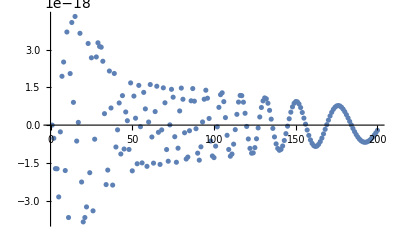

```mathematica
ListPlot[Table[NIntegrate[Subscript[A, v,III][a0,a1,1]*Subscript[A, v,III][a1,a2,b1/2]*ϕintegral[a0,a1,a2,1,b1/2,ϕ0,ϕ2]/.{a0->20,a2->20,ϕ0->1,ϕ2->5},{a1,1/4,Infinity},Method->"AdaptiveQuasiMonteCarlo"],{b1,1,200}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.999465}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.952027}. NIntegrate obtained -2.56983×10^-19-1.15911×10^-18 ⅈ and 2.46271×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in a1 near {a1} = {0.952152}. NIntegrate obtained -4.86479×10^-19+3.32543×10^-18 ⅈ and 6.02549×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

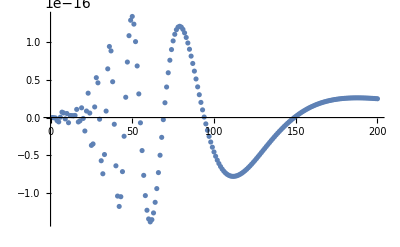

```mathematica
ListPlot[Table[NIntegrate[Subscript[A, v,III][a0,a1,b1/2]*Subscript[A, v,III][a1,a2,b1/2]*ϕintegral[a0,a1,a2,b1/2,b1/2,ϕ0,ϕ2]/.{a0->20,a2->20,ϕ0->1,ϕ2->5},{a1,1/4,Infinity},Method->"AdaptiveQuasiMonteCarlo"],{b1,1,200}]]
```

### Partition sum with non-equidistant spectrum

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][a0,a1,1/2+Exp[b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[b],0,dϕ]]],{b,-5,20},PlotRange->All],{a0,1,10},{a1,1,30},{dϕ,0,10}]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+(200M)/b]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+(200M)/b,0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,1,2*200M}],{M,1,10}]
```

{1.24007×10^-7,2.48035×10^-7,3.72061×10^-7,4.96086×10^-7,6.20111×10^-7,7.44136×10^-7,8.68162×10^-7,9.92187×10^-7,1.11621×10^-6,1.24024×10^-6}

Saddle point at -3 on the x-axis below

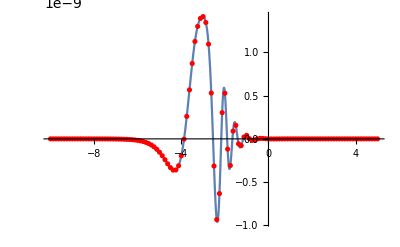

```mathematica
Show[Plot[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-10,5},PlotRange->All],ListPlot[Table[{b/8,N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7}},{b,-80,40}],PlotRange->All,PlotStyle->Red]]
```

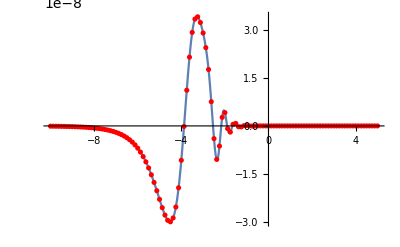

```mathematica
Show[Plot[N[(1/2+Exp[-b])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-10,5},PlotRange->All],ListPlot[Table[{b/8,N[(1/2+Exp[-b/8])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7}},{b,-80,40}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Z=Sum[N[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,40}]
Zb=Sum[N[(1/2+Exp[-b/8])*Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,40}]
```

5.64384×10^-9+9.81354×10^-9 ⅈ

-1.40298×10^-7+2.26092×10^-7 ⅈ

```mathematica
Zb/Z
```

11.1342+20.6997 ⅈ

```mathematica
1/2+Exp[-19.383500026494147/(-4)]
```

127.715

Saddle point at -0.75 on the x-axis below

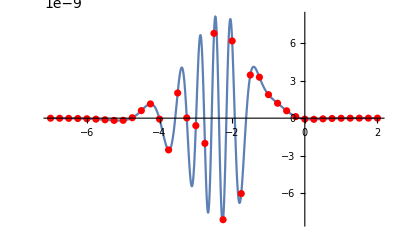

```mathematica
Show[Plot[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-7,2},PlotRange->All],ListPlot[Table[{b/4,N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2}},{b,-28,8}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-40,n}],{n,5,30}]
```

{6.99066×10^-9,6.99202×10^-9,6.99388×10^-9,6.9956×10^-9,6.997×10^-9,6.99809×10^-9,6.99893×10^-9,6.99956×10^-9,7.00005×10^-9,7.00041×10^-9,7.00069×10^-9,7.00091×10^-9,7.00107×10^-9,7.0012×10^-9,7.0013×10^-9,7.00137×10^-9,7.00143×10^-9,7.00148×10^-9,7.00151×10^-9,7.00154×10^-9,7.00156×10^-9,7.00158×10^-9,7.00159×10^-9,7.0016×10^-9,7.00161×10^-9,7.00162×10^-9}

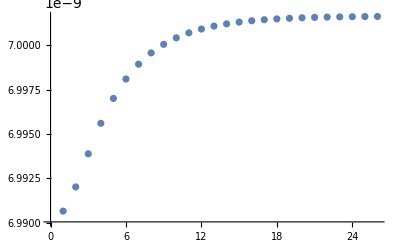

```mathematica
ListPlot[%166]
```

```mathematica
Table[Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/4]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/4],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,n,30}],{n,-40,-20}]
```

{7.00162×10^-9,7.00162×10^-9,7.00163×10^-9,7.00165×10^-9,7.00169×10^-9,7.00174×10^-9,7.00183×10^-9,7.00199×10^-9,7.00226×10^-9,7.00272×10^-9,7.00353×10^-9,7.00494×10^-9,7.00744×10^-9,7.01189×10^-9,7.01991×10^-9,7.03439×10^-9,7.06046×10^-9,7.10675×10^-9,7.18632×10^-9,7.31419×10^-9,7.49252×10^-9}

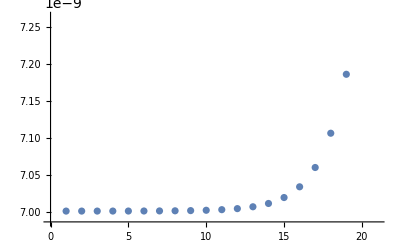

```mathematica
ListPlot[%169]
```

We find satisfactory convergence for a lower cutoff n=-30 and upper cutoff n=30

Expectation value of b

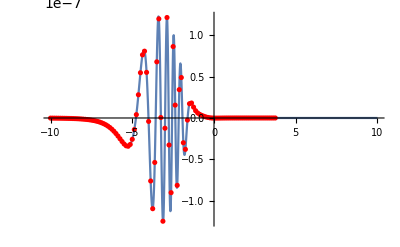

```mathematica
Show[Plot[N[Re[(1/2+Exp[-b])Subscript[A, v,III][a0,a1,1/2+Exp[-b]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-10,10},PlotRange->All],ListPlot[Table[{b/8,N[Re[(1/2+Exp[-b/8])Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2}},{b,-80,30}],PlotRange->All,PlotStyle->Red]]
```

```mathematica
Z=Sum[N[Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->30,dϕ->1.7},{b,-80,80}]
Zb=Sum[N[(1/2+Exp[-b/8])Re[Subscript[A, v,III][a0,a1,1/2+Exp[-b/8]]*Exp[-I*Subscript[S, ϕ,tl][a0,a1,1/2+Exp[-b/8],0,dϕ]]]]/.{a0->10,a1->20,dϕ->2},{b,-80,80}]
```

## Introducing a mass

### Mass dependence of strut length solution

```mathematica
Manipulate[Plot[(Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,ϕ1,ϕ1+2,10^logm]/.{a0->10,a1->30}),{b,1/2,50}],{ϕ1,0,5},{logm,-5,5}]
```

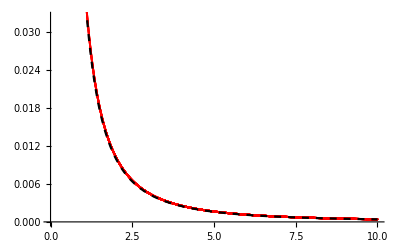

```mathematica
bsolsmass=Table[{10^-3*n,b/.FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30})==0,{b,14}]},{n,1,10^4}];
Show[{ListPlot[bsolsmass,PlotStyle->Red],Plot[a*x^-2/.{a->0.04},{x,10^-3,10},PlotStyle->{Black,Dashed}]}]
```

The relation of classical struts and the mass is b ~ 1/m^2. The proportionality factor depends on the ϕ’s and on the a’s

### Mass-dependent expectation value in Sector III with a_0= 10, a_1 = 30, ϕ_0 = 2, ϕ_1= 4

```mathematica
bsolsmass[[50]]
```

{1/20,5.8332}

```mathematica
Manipulate[Plot[Re[Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]]/.{a0->10,a1->30},{b,1,200}],{n,1,10^4}]
```

```mathematica
NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->50}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
```

1.34481×10^-9+6.03878×10^-10 ⅈ

8.23787×10^-9+2.67174×10^-9 ⅈ

```mathematica
(8.237868210622867*^-9+2.6717397439233075*^-9 ⅈ)/(1.3448114034420642*^-9+6.038775063261134*^-10 ⅈ)
```

5.84017-0.635784 ⅈ

The expectation value from the timelike path integral yields a value close to the classical one, b = 5.8332! The relative error is 0.1%

```mathematica
Zmass=Table[NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,1,10}]
Zbmass=Table[NSum[(b/2 Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,1,10}]
```

{-1.4381×10^-8-3.71424×10^-10 ⅈ,-4.87157×10^-9-7.02217×10^-9 ⅈ,2.77791×10^-11-4.81422×10^-9 ⅈ,1.91939×10^-9-1.86165×10^-9 ⅈ,1.34481×10^-9+6.03878×10^-10 ⅈ,-3.96909×10^-10+7.05887×10^-10 ⅈ,-2.11689×10^-10-3.91653×10^-10 ⅈ,-1.20456×10^-8+1.88472×10^-8 ⅈ,-7.81474×10^-9-4.60492×10^-9 ⅈ,-2.63918×10^-9+3.83599×10^-9 ⅈ}

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

{-1.73951×10^-7+1.61756×10^-8 ⅈ,-5.61663×10^-8-6.61933×10^-8 ⅈ,-3.50092×10^-9-4.02444×10^-8 ⅈ,1.20765×10^-8-1.42476×10^-8 ⅈ,8.23787×10^-9+2.67174×10^-9 ⅈ,-1.53183×10^-9+3.74062×10^-9 ⅈ,-1.13483×10^-9-1.53218×10^-9 ⅈ,-3.21588×10^-7+5.08036×10^-7 ⅈ,-1.1132×10^-7-6.34298×10^-8 ⅈ,-2.7611×10^-8+4.07077×10^-8 ⅈ}

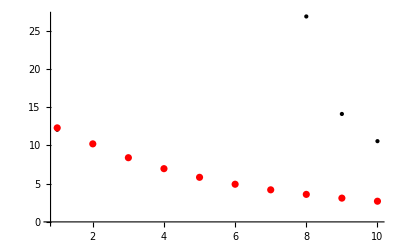

```mathematica
bexpvalsmass=Table[Zbmass[[i]]/Zmass[[i]],{i,1,10}];
ListPlot[{Re[bexpvalsmass[[1;;10]]],Table[bsolsmass[[10n,2]],{n,1,10}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

Good agreement for small masses. Larger masses seem to require a refined spectrum

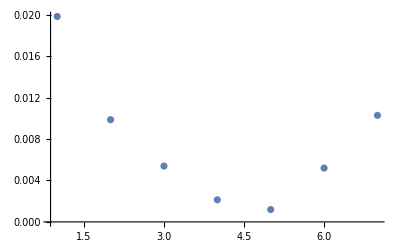

```mathematica
ListPlot[Table[(Abs[Re[bexpvalsmass[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotRange->All]
```

Relative error small in the region where mass is not too small and too large

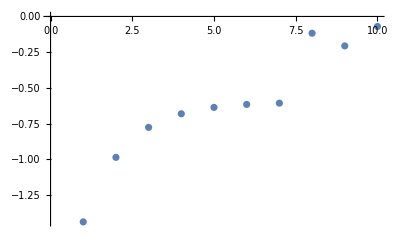

```mathematica
ListPlot[Im[bexpvalsmass]]
```

Imaginary part seems to converge to a certain value for larger masses

```mathematica
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.1}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]/NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.1}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30,n->0.1})==0,{b,14}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

13.0709-1.91662 ⅈ

```mathematica
{b->13.53569069238456}
```

```mathematica
(13.53569069238456-13.070885579830666)/13.53569069238456
```

0.0343392

```mathematica
NSum[(b/2*Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.01}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]/NSum[(Subscript[A, v,III][a0,a1,b/2]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/2,2,4,10^-3*n]]/.{a0->10,a1->30,n->0.01}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"]
FindRoot[(4*(Pi/2-ArcCos[(a0-a1)^2/(4 b^2+(a0-a1)^2)])+D[Subscript[S, ϕ,tl][a0,a1,b,2,4,10^-3*n],b]/.{a0->10,a1->30,n->0.01})==0,{b,14}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

13.0707-1.91769 ⅈ

{b→13.5358}

```mathematica
(13.535842066846781-13.070695511810023)/13.535842066846781
```

0.0343641

The expectation value converges in the limit m → 0 to a value that is close the classical value. Therefore, we have the situation where lim_(m→0^+) b(m)≠b(m=0). The relative error of classical value and expectation value is still small with ~3%.

### Refining the spectrum

For the given boundary data, the expectation value deviates from classical value for masses m = 0.08. We suspect this to arise from a spectrum that is too coarse to capture the saddle point

```mathematica
ZmassRef=Table[NSum[(Subscript[A, v,III][a0,a1,b/20]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/20,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,8,20}]
ZbmassRef=Table[NSum[(b/20 Subscript[A, v,III][a0,a1,b/20]*Exp[I*Subscript[S, ϕ,tl][a0,a1,b/20,2,4,10^-3*(10*n)]]/.{a0->10,a1->30}),{b,1,Infinity},NSumTerms->100,Method->"WynnEpsilon"],{n,8,20}]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

{2.14176×10^-9+1.21111×10^-9 ⅈ,-1.28249×10^-9-4.89154×10^-10 ⅈ,6.46215×10^-10+4.28916×10^-10 ⅈ,-1.84396×10^-10-4.05128×10^-10 ⅈ,-1.09669×10^-10+2.35729×10^-10 ⅈ,1.54777×10^-10+9.0674×10^-13 ⅈ,-1.5603×10^-11-9.26902×10^-11 ⅈ,-5.79517×10^-11+5.82232×10^-12 ⅈ,-7.0037×10^-12+3.61494×10^-11 ⅈ,1.82189×10^-11+1.52218×10^-11 ⅈ,1.5386×10^-11-2.58721×10^-12 ⅈ,7.02116×10^-12-7.73148×10^-12 ⅈ,1.82657×10^-12-6.87749×10^-12 ⅈ}

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

{8.57086×10^-9+3.14348×10^-9 ⅈ,-4.38442×10^-9-7.89069×10^-10 ⅈ,2.06872×10^-9+8.14409×10^-10 ⅈ,-7.00409×10^-10-8.96476×10^-10 ⅈ,-1.0377×10^-10+5.88798×10^-10 ⅈ,3.10453×10^-10-8.8973×10^-11 ⅈ,-8.1895×10^-11-1.59526×10^-10 ⅈ,-9.3054×10^-11+4.25002×10^-11 ⅈ,9.29474×10^-12+5.91871×10^-11 ⅈ,3.40154×10^-11+1.17309×10^-11 ⅈ,1.89245×10^-11-1.14771×10^-11 ⅈ,4.72587×10^-12-1.31004×10^-11 ⅈ,-1.26572×10^-12-8.86326×10^-12 ⅈ}

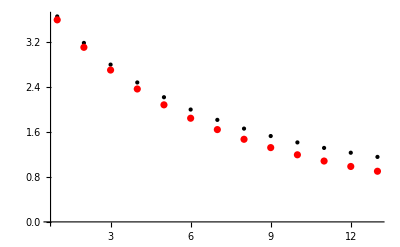

```mathematica
bexpvalsmassRef=Table[ZbmassRef[[i]]/ZmassRef[[i]],{i,1,13}];
ListPlot[{Re[bexpvalsmassRef[[1;;13]]],Table[bsolsmass[[10n,2]],{n,8,20}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

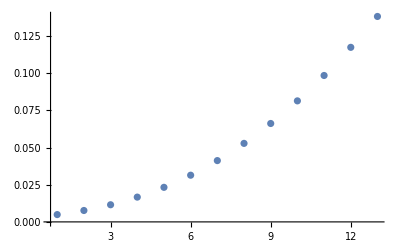

```mathematica
ListPlot[Table[(Abs[Re[bexpvalsmassRef[[i]]]-bsolsmass[[10*(7+i),2]]])/bsolsmass[[10*i,2]],{i,1,13}],PlotRange->All]
```

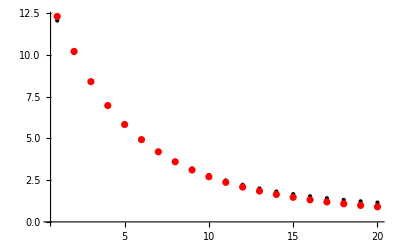

```mathematica
Join[bexpvalsmass[[1;;7]],bexpvalsmassRef];
ListPlot[{Re[Join[bexpvalsmass[[1;;7]],bexpvalsmassRef]],Table[bsolsmass[[10n,2]],{n,1,20}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

Combined results of unrefined and refined (for n  > 8)

### Saddle points in I and II

```mathematica
Manipulate[Plot[Subscript[S, III][a0,a1,b]+Subscript[S, ϕ,tl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},{b,1/2,20}],{logm,-5,5}]
```

```mathematica
Manipulate[Plot[Piecewise[{{Subscript[S, I][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},√((10-30)^2/4)<b<√((10-30)^2/2)},{Subscript[S, II][a0,a1,b]+Subscript[S, ϕ,sl][a0,a1,b,2,4,10^logm]/.{a0->10,a1->30},0<b<√((10-30)^2/4)}}],{b,0,√((10-30)^2/2)},Epilog->InfiniteLine[{{√((10-30)^2/4),0},{-1,1}}]],{logm,-5,5}]
```

```mathematica
Manipulate[Plot[Subscript[S, I][a0,a1,-b]-Subscript[S, ϕ,sl][a0,a1,-b,2,4,10^logm]/.{a0->10,a1->30},{b,-√((10-30)^2/2),-√((10-30)^2/4)}],{logm,-5,3}]
```

### Including Sectors I and II

```mathematica
Manipulate[Plot[Re[Piecewise[{{Subscript[A, v,I][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-2*n]],-√((10-30)^2/2)<b<-√((10-30)^2/4)},{Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-2*n]],-√((10-30)^2/4)<b<0}}]],{b,-√((10-30)^2/2),0},Epilog->InfiniteLine[{{-√((10-30)^2/4),0},{-1,1}}]],{n,1,10}]
```

There is a new problem arising: the kinetic term of the scalar field diverges as the Euclidean configurations are approached. Let’s first consider Sector II:

```mathematica
Table[NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*5)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive",MinRecursion->n,MaxRecursion->11,Exclusions->{b==-√((10-30)^2/4)}],{n,1,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 3 recursive bisections in b near {b} = {-10.}. NIntegrate obtained -2.54468×10^-16+1.67184×10^-16 ⅈ and 7.79454×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 2 recursive bisections in b near {b} = {-9.99997}. NIntegrate obtained -3.34077×10^-15+2.19961×10^-15 ⅈ and 1.02397×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in b near {b} = {-9.99964}. NIntegrate obtained -4.35562×10^-14+2.93862×10^-14 ⅈ and 1.3452×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06753×10^-12+2.31661×10^-12 ⅈ,2.06756×10^-12+2.31659×10^-12 ⅈ,2.06788×10^-12+2.31638×10^-12 ⅈ}

```mathematica
ZmassII=Table[NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive",MinRecursion->9,Exclusions->{b==-√((10-30)^2/4)}],{n,1,10}];
ZbmassII=Table[NIntegrate[(-b)Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive",MinRecursion->9,Exclusions->{b==-√((10-30)^2/4)}],{n,1,10}];
bexpvalsmassIIandIII=Table[(ZbmassII+Zbmass)[[i]]/(Zmass+ZmassII)[[i]],{i,1,10}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained 2.15465×10^-12-1.61609×10^-12 ⅈ and 7.06808×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained 1.24389×10^-12-2.38427×10^-12 ⅈ and 7.06806×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained -1.89393×10^-12+1.89904×10^-12 ⅈ and 7.06802×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained 2.15272×10^-11-1.61425×10^-11 ⅈ and 7.06808×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained 1.24295×10^-11-2.38177×10^-11 ⅈ and 7.06806×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in b near {b} = {-9.98047}. NIntegrate obtained -1.89231×10^-11+1.89693×10^-11 ⅈ and 7.06802×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

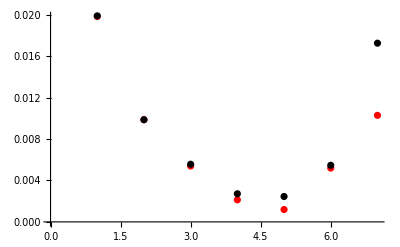

```mathematica
Show[{ListPlot[Table[(Abs[Re[bexpvalsmass[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotStyle->Red],ListPlot[Table[(Abs[Re[bexpvalsmassIIandIII[[i]]]-bsolsmass[[10*i,2]]])/bsolsmass[[10*i,2]],{i,1,7}],PlotStyle->Black]}]
```

The deviations are a signature of a saddle point that can be present in Sector II for certain mass values

```mathematica
Table[Abs[Re[bexpvalsmassIIandIII[[i]]-bexpvalsmass[[i]]]]/Re[bexpvalsmassIIandIII[[i]]],{i,1,10}]
```

{0.000180788,0.000116428,0.000589358,0.00685827,0.0153922,0.00957185,0.0293785,0.0000895943,0.0000836529,0.0000547322}

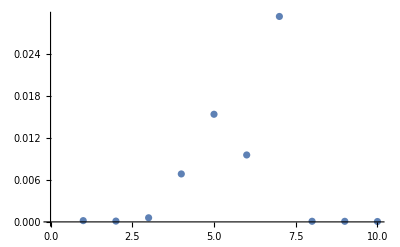

```mathematica
ListPlot[{0.0001807880513017232,0.00011642762278823651,0.0005893580782644416,0.0068582671006395274,0.015392178091081543,0.009571850124941524,0.02937846923738023,0.00008959434590725006,0.00008365292390453275,0.0000547322267917954}]
```

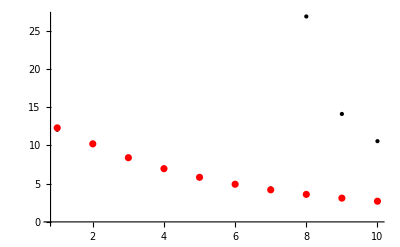

```mathematica
bexpvalsmassIIandIII=Table[(ZbmassII+Zbmass)[[i]]/(Zmass+ZmassII)[[i]],{i,1,10}];
ListPlot[{Re[bexpvalsmassIIandIII[[1;;10]]],Table[bsolsmass[[10n,2]],{n,1,10}]},PlotRange->All,PlotStyle->{{Black,PointSize[Large],Opacity[1]},{Red}}]
```

```mathematica
ZmassI=Table[NIntegrate[Subscript[A, v,I][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];
ZbmassI=Table[NIntegrate[(-b)Subscript[A, v,I][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/2),-√((10-30)^2/4)},Exclusions->{b==-√((10-30)^2/2)},Method->"LocalAdaptive"],{n,1,10}];
ZmassII=Table[NIntegrate[Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive"],{n,1,10}];
ZbmassII=Table[NIntegrate[(-b)Subscript[A, v,II][10,30,-b]*Exp[I*Subscript[S, ϕ,sl][10,30,-b,2,4,10^-3(10*n)]],{b,-√((10-30)^2/4),0},Method->"LocalAdaptive"],{n,1,10}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421356237309504954561254915878895065770447542119992732898547}. NIntegrate obtained 3.4268×10^-18+1.64796×10^-17 ⅈ and 1.46933×10^-16 for the integral and error estimates.

Power::infy: Infinite expression 1/(√(0``-347.07627035644333+0``-366.2032519125639 ⅈ)) encountered.

Power::infy: Infinite expression 1/(√(0``-286.26539094715207+0``-302.3518285328082 ⅈ)) encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421356237309504954561254915878895065770447542119992732898547}. NIntegrate obtained 6.42996×10^-18+1.32469×10^-17 ⅈ and 1.49031×10^-16 for the integral and error estimates.

Power::infy: Infinite expression 1/(√(0``-347.07627035644333+0``-366.2032519125639 ⅈ)) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {-14.1421356237309504954561254915878895065770447542119992732898547}. NIntegrate obtained 1.08351×10^-17+7.23136×10^-18 ⅈ and 1.52421×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

Mathematica has detected an internal error:
  iCopyExpr() called on symbol.

Please report this error as soon as possible to
support@wolfram.com giving as many details as possible
of the circumstances under which it occurred.

### Comparison to continuum measure